# Population Dynamics Model for a Multi-Step Evolution of Gynogenesis in the A. Molly

## Mating probabilities and death rates

Here we consider a system with three species: P. mex (m), P. lat (l) and a hybrid species (h).

We note :

```mathematica
Subscript[Φ, i,j] : Mating rate of females from species i with male from species j. Because we assume that  Subscript[N, m] = Subscript[N, l] at all time, we can demonstrate that:
```

```mathematica
Subscript[Φ, mm]=Subscript[c, p];
Subscript[Φ, ll]=Subscript[c, p];
Subscript[Φ, ml]=1-Subscript[c, p];
Subscript[Φ, lm]=1-Subscript[c, p];
```

```mathematica
Subscript[Ψ, i] : Death rate of individuals from species i, with K the carrying capacity of the environment, assumed equal for all species:
```

```mathematica
Subscript[Ψ, m]=(2 Subscript[N, m])/K;
Subscript[Ψ, l]=(2 Subscript[N, l])/K;
Subscript[Ψ, h]=(N_(h1,♀)+N_(h1,♂)+N_(h2,♀)+N_(h2,♂))/K;
```

## Parent Equilibrium

Parental System ODEs:

```mathematica
Subscript[g, m]=(1/2 Subscript[Φ, mm]-Subscript[Ψ, m])Subscript[N, m];
Subscript[g, l] = (1/2 Subscript[Φ, ll]-Subscript[Ψ, l])Subscript[N, l];
```

To get the equilibrium of the parent system (which do not depend on hybrids), we solve their corresponding ODEs:

```mathematica
Solve[Subscript[g, m]==0&&Subscript[g, l] ==0&&Subscript[N, m]>0&&Subscript[N, l]>0&&K>0&&1≥Subscript[c, p]≥0,{Subscript[N, m],Subscript[N, l]}]
```

{{N_m→ConditionalExpression[(K c_p)/4, K>0&&0<c_p<1],N_l→ConditionalExpression[(K c_p)/4, K>0&&0<c_p<1]}}

In the Appendix, we show that this equilibrium is trivially stable.

In the following, we will simply assume that the parent populations are at constant size (K c_p)/4 at all times.

## Model 1: Sperm Failure

## Dynamical Equations

g_i : growth function of population of class i.  6 classes in total: 
mex, lat, female wild-type hybrid, male wild-type hybrid, female mutant hybrid, male mutant hybrid.

```mathematica
g_(h1,♀)=(Subscript[Φ, ml] Subscript[N, m])/2 + (Subscript[Φ, lm] Subscript[N, l])/2+((1-Subscript[Φ, hh])/2-Subscript[Ψ, h])N_(h1,♀)+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀);
g_(h1,♂)=(Subscript[Φ, ml] Subscript[N, m])/2+ (Subscript[Φ, lm] Subscript[N, l])/2+((1-Subscript[Φ, hh])/2 N_(h1,♀)-Subscript[Ψ, h] N_(h1,♂))+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀);
g_(h2,♀)=((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-Subscript[Ψ, h])N_(h2,♀);
g_(h2,♂)=(1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂);
```

## Wild - type hybrid initial equilibrium (wt)

### Equilibrium expression

We obtain the wild-type equilibrium in the absence of mutant hybrids by solving the ODEs assuming: (1) parents are at their equilibrium, (2) N_(h2,♀) = N_(h2,♂) = 0, and (3) N_(h1,♂) = N_(h1,♀) (because we assume that wild-type hybrids are entirely sexual and produced with unbiased sex-ratios.

```mathematica
Solve[(g_(h1,♀)/.N_(h2,♀)->0/.N_(h2,♂)->0/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.N_(h1,♂)->N_(h1,♀))==0&&K>0&&1>Subscript[c, p]>0&&1>Subscript[Φ, hh]>0&&N_(h1,♀)>0,{N_(h1,♀)},Reals]//FullSimplify
```

{{N_(h1,♀)→ConditionalExpression[1/8 K (1+√(-8 (-1+c_p) c_p+(-1+Φ_hh)^2)-Φ_hh), 0<c_p<1&&0<Φ_hh<1&&K>0]}}

### Equilibrium Stability

The stability of this equilibrium is determines by calculating the sign of (∂g_(h1,♀))/(∂N_(h1,♀)):

```mathematica
D[g_(h1,♀)/.N_(h2,♀)->0/.N_(h2,♂)->0/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.N_(h1,♂)->N_(h1,♀),N_(h1,♀)]/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])//FullSimplify
```

-1/2 √(-8 (-1+c_p) c_p+(-1+Φ_hh)^2)

This is always negative : the equilibrium is stable.

### Φ_hh

We can calculate Φ_hh at this equilibrium:

```mathematica
Solve[Subscript[Φ, hh]==((Subscript[c, h] N_(h1,♂))/(Subscript[c, h] N_(h1,♂)+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.N_(h1,♂)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh]))&&K>0&&1>Subscript[c, p]>0&&1>Subscript[c, h]>0,Subscript[Φ, hh],Reals]
```

{{Φ_hh→ConditionalExpression[Root[-c_h^2+#1^3 (-c_h+c_h^2)+c_h^2 c_p+#1 (-c_h+3 c_h^2-2 c_h^2 c_p)+#1^2 (2 c_h-3 c_h^2+2 c_p-4 c_h c_p+3 c_h^2 c_p)&,2], 0<c_h<1&&0<c_p<1&&K>0]}}

We can not obtain an analytical expression for Φ_hh at the wild-type equilibrium without mutants - we only know that it must be the second solution of a third order polynomial.

### Population Size and Φ_hh Numerical Calculations at equilibrium

Φ_hh and Nh1 can be calculated numerically:

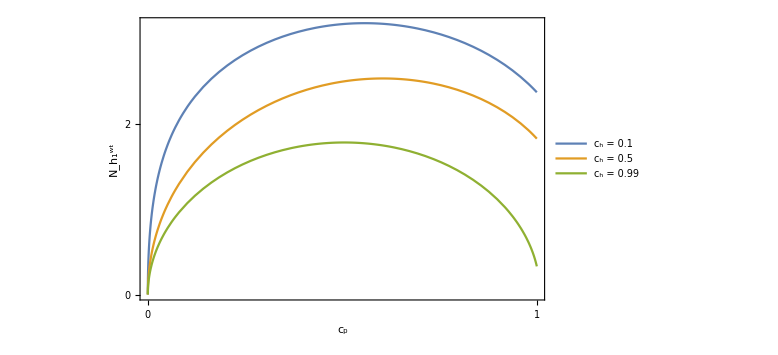

```mathematica
Plot[{1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.K->10/.Subscript[c, h]->0.1,1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.K->10/.Subscript[c, h]->0.5,1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.K->10/.Subscript[c, h]->0.99},{Subscript[c, p],0,1},Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{{{0,2},None},{{0,1},None}},ImageSize->Large,LabelStyle->Directive[Bold, 18],FrameLabel->{"c_p","N_h_1^wt"},RotateLabel->False,PlotLegends->{"c_h = 0.1","c_h = 0.5","c_h = 0.99"}]
```

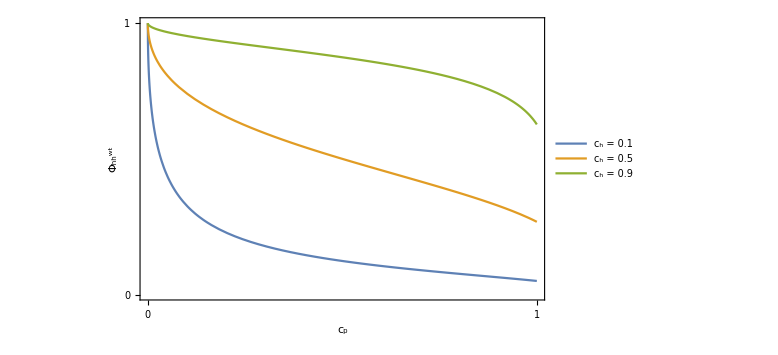

```mathematica
Plot[{Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.K->10/.Subscript[c, h]->0.1,Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.K->10/.Subscript[c, h]->0.5,Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.K->10/.Subscript[c, h]->0.9},{Subscript[c, p],0,1},Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{{{0,1},None},{{0,1},None}},ImageSize->Large,LabelStyle->Directive[Bold, 18],FrameLabel->{"c_p","Φ_hh^wt"},RotateLabel->False,PlotLegends->{"c_h = 0.1","c_h = 0.5","c_h = 0.9"}]
```

## Conditions for the Spread of a Partial Apomictic Mutant h2 at wt equilibrium

### For any values of β and σ

```mathematica
Reduce[(((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-Subscript[Ψ, h])/.N_(h2,♂)->0/.N_(h2,♀)->0/.N_(h1,♂)->N_(h1,♀))>0&&N_(h1,♀)>0&&K>0&&1>Subscript[c, p]>0&&1>Subscript[Φ, hh]>1/3&&1≥Subscript[α, 2]≥0&&1≥Subscript[β, 2]≥0&&1≥Subscript[σ, 2]≥-1,Subscript[α, 2],Reals]//FullSimplify
```

N_(h1,♀)>0&&c_p>0&&3 Φ_hh>1&&c_p<1&&Φ_hh<1&&α_2≤1&&((β_2==0&&((σ_2==1&&((K+(4 N_(h1,♀))/(-1+Φ_hh)==0&&α_2>0)||(K+(4 N_(h1,♀))/(-1+Φ_hh)>0&&α_2≥0)||((K-K Φ_hh-4 N_(h1,♀))/(K-3 K Φ_hh)<α_2&&(2 N_(h1,♀))/Φ_hh<K&&K+(4 N_(h1,♀))/(-1+Φ_hh)<0)))||(1+σ_2>0&&σ_2<1&&((K+(8 N_(h1,♀))/((1+σ_2) (-1+Φ_hh))>0&&α_2≥0)||((4 N_(h1,♀))/(Φ_hh+σ_2 Φ_hh)<K&&(K (1+σ_2) (-1+Φ_hh)+8 N_(h1,♀))/(K (1+σ_2) (-1+3 Φ_hh))<α_2&&K+(8 N_(h1,♀))/((1+σ_2) (-1+Φ_hh))≤0)))))||(1+σ_2>0&&σ_2≤1&&((β_2<1&&β_2>0&&((K==(8 N_(h1,♀))/((-1+β_2) (1+σ_2) (-1+Φ_hh))&&α_2>0)||(K+(4 N_(h1,♀))/((1+σ_2) (β_2 (-1+Φ_hh)-Φ_hh))>0&&K<(8 N_(h1,♀))/((-1+β_2) (1+σ_2) (-1+Φ_hh))&&(K (-1+β_2) (1+σ_2) (-1+Φ_hh)-8 N_(h1,♀))/(K (1+σ_2) (1+3 β_2 (-1+Φ_hh)-3 Φ_hh))<α_2)||(K>(8 N_(h1,♀))/((-1+β_2) (1+σ_2) (-1+Φ_hh))&&α_2≥0)))||(β_2==1&&K>(4 N_(h1,♀))/(1+σ_2)&&α_2>(4 N_(h1,♀))/(K+K σ_2)))))

### For β = 0 and σ = 0

We prove in the main text that a first mutant h2 must be partially apomictic to have a chance to spread. We consider that the effect of the mutation is to only introduce some rate of apomixis. Such a mutant spreads if and only if g_(h2,♀)>0, which we prove in the main text may be possible only if Φ_hh>1/3:

```mathematica
Reduce[(((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-Subscript[Ψ, h])/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.N_(h2,♂)->0/.N_(h2,♀)->0/.N_(h1,♂)->N_(h1,♀))>0&&N_(h1,♀)>0&&K>0&&1>Subscript[c, p]>0&&1>Subscript[Φ, hh]>1/3&&1≥Subscript[α, 2]≥0,Subscript[α, 2],Reals]//FullSimplify
```

N_(h1,♀)>0&&0<c_p<1&&1/3<Φ_hh<1&&((K>-(8 N_(h1,♀))/(-1+Φ_hh)&&0≤α_2≤1)||((4 N_(h1,♀))/Φ_hh<K≤-(8 N_(h1,♀))/(-1+Φ_hh)&&(K-K Φ_hh-8 N_(h1,♀))/(K-3 K Φ_hh)<α_2≤1))

The partially apomictic mutant spreads if and only if α_2 is sufficiently large. We note α* the minimum value of α_2 for the mutant to spread. α* = (K(1- Φ_hh)-8 N_(h1,♀))/(K(1-3 Φ_hh))

We can calculate α_lim numerically, knowing that N_(h1,♀) and Φ_hh are at the wt equilibrium determined above:

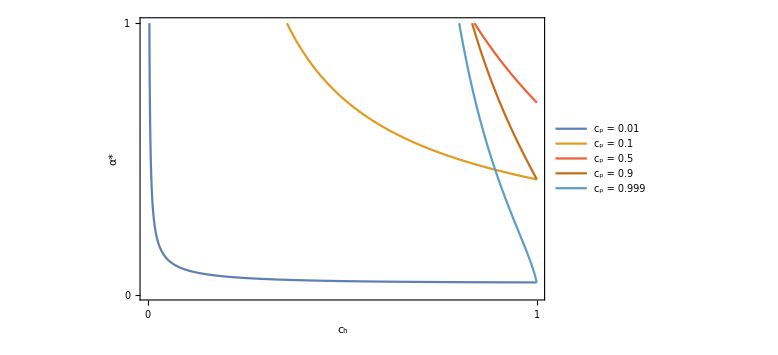

```mathematica
A1=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c, p]->0.001/.K->10},{Subscript[c, h],0.004,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[1]],FrameStyle->Thick,FrameLabel->{"c_h","α*"},RotateLabel->False,PlotLegends->{"c_p = 0.01"},ImageSize->Large,LabelStyle->Directive[20,Bold,Black],FrameTicks->{{{0,1},None},{{0,1},None}}];
A2=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, p]->0.1/.K->10},{Subscript[c, h],0.2,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"c_p = 0.1"},LabelStyle->Directive[20,Bold,Black]];
A3=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, p]->0.3/.K->10},{Subscript[c, h],0.5,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[3]],PlotLegends->{"c_p = 0.3"},LabelStyle->Directive[20,Bold,Black]];
A4=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, p]->0.5/.K->10},{Subscript[c, h],0.6,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[4]],PlotLegends->{"c_p = 0.5"},LabelStyle->Directive[20,Bold,Black]];
A5=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, p]->0.7/.K->10},{Subscript[c, h],0.7,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[5]],PlotLegends->{"c_p = 0.7"},LabelStyle->Directive[20,Bold,Black]];
A6=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, p]->0.9/.K->10},{Subscript[c, h],0.7,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[6]],PlotLegends->{"c_p = 0.9"},LabelStyle->Directive[20,Bold,Black]];
A7=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c,p]->0.999/.K->10},{Subscript[c, h],0.7,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[7]],PlotLegends->{"c_p = 0.999"},LabelStyle->Directive[20,Bold,Black]];
Fig=Show[{A1,A2,A4,A6,A7}]
```

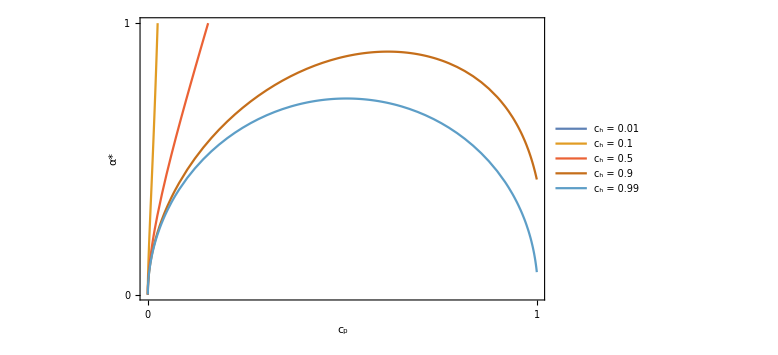

```mathematica
A1=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c, h]->0.01/.K->10},{Subscript[c, p],0.0,0.0000001},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[1]],FrameStyle->Thick,FrameLabel->{"c_p","α*"},RotateLabel->False,PlotLegends->{"c_h = 0.01"},ImageSize->Large,LabelStyle->Directive[20,Bold,Black],FrameTicks->{{{0,1},None},{{0,1},None}}];
A2=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.1/.K->10},{Subscript[c, p],0.0,0.05},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"c_h = 0.1"},LabelStyle->Directive[20,Bold,Black]];
A3=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.3/.K->10},{Subscript[c, p],0.0,0.4},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[3]],PlotLegends->{"c_h = 0.3"},LabelStyle->Directive[20,Bold,Black]];
A4=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.5/.K->10},{Subscript[c, p],0.0,0.6},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[4]],PlotLegends->{"c_h = 0.5"},LabelStyle->Directive[20,Bold,Black]];
A5=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.7/.K->10},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[5]],PlotLegends->{"c_h = 0.7"},LabelStyle->Directive[20,Bold,Black]];
A6=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.9/.K->10},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[6]],PlotLegends->{"c_h = 0.9"},LabelStyle->Directive[20,Bold,Black]];
A7=Plot[{(K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c, h]->0.99/.K->10},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[7]],PlotLegends->{"c_h = 0.99"},LabelStyle->Directive[20,Bold,Black]];
Fig=Show[{A1,A2,A4,A6,A7}]
```

The partially apomictic mutant can spread at least for some values of α_2 if and only if Φ_hh > 1/3 and α_lim < 1:

```mathematica
Reduce[(Subscript[Φ, hh]/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2])>1/3&&((K-K Subscript[Φ, hh]-8 N_(h1,♀))/(K-3 K Subscript[Φ, hh])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2])<1&&K>0&&1>Subscript[c, p]>0&&0<Subscript[c, h]<1,Subscript[c, h]]//FullSimplify
```

K>0&&0<c_p<1&&√((c_p^2+16 c_p^3-16 c_p^4)/(1+2 c_p (2+5 c_p))^2)+(c_p (3+8 c_p))/(1+2 c_p (2+5 c_p))<c_h<1

The partially apomictic mutant can spread at least for some values of α_2 if and only if c_h is sufficiently large, larger than an expression determined by c_p. Assortative mating within mutants favours the spread of the partially apomictic mutant.

```mathematica
FullSimplify[√((Subscript[c, p]^2+16 Subscript[c, p]^3-16 Subscript[c, p]^4)/(1+2 Subscript[c, p] (2+5 Subscript[c, p]))^2)+(Subscript[c, p] (3+8 Subscript[c, p]))/(1+2 Subscript[c, p] (2+5 Subscript[c, p])),Subscript[c, p]>0]
```

(c_p (3+8 c_p+√(1-16 (-1+c_p) c_p)))/(1+2 c_p (2+5 c_p))

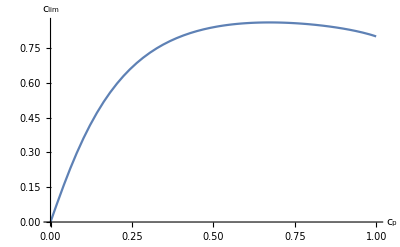

```mathematica
Plot[(Subscript[c, p] (3+8 Subscript[c, p]+√(1-16 (-1+Subscript[c, p]) Subscript[c, p])))/(1+2 Subscript[c, p] (2+5 Subscript[c, p])),{Subscript[c, p],0,1},AxesLabel->{"c_p","c_lim"}]
```

## Wild - Type - Mutant Equilibrium

When the first apomictic mutant spreads, it can reach an equilibrium that we found by solving the ODEs assuming that (1) N_(h1,♂) = N_(h1,♀), and (2) N_(h2,♂) = N_(h2,♀).

```mathematica
Solve[(g_(h1,♀)/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.N_(h1,♂)->N_(h1,♀)/.N_(h2,♂)->N_(h2,♀))==0&&(g_(h2,♀)/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.N_(h1,♂)->N_(h1,♀)/.N_(h2,♂)->N_(h2,♀))==0&&K>0&&1>Subscript[c, p]>0&&1>Subscript[Φ, hh]>1/3&&1≥Subscript[α, 2]≥0&&N_(h2,♀)≠0,{N_(h1,♀),N_(h2,♀)},Reals]//FullSimplify
```

{{N_(h1,♀)→ConditionalExpression[(K (-8 (-1+c_p) c_p+(-1+α_2) (-1+Φ_hh) (1-Φ_hh+α_2 (-1+3 Φ_hh))))/(16 α_2 (-1+2 Φ_hh)), ],N_(h2,♀)→ConditionalExpression[(K (8 (-1+c_p) c_p+α_2^2 (1-3 Φ_hh)^2-(-1+Φ_hh)^2))/(16 α_2 (-1+2 Φ_hh)), ]}}

Total amount of hybrid males and females in this case is:

```mathematica
(K (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[α, 2]) (-1+Subscript[Φ, hh]) (1-Subscript[Φ, hh]+Subscript[α, 2] (-1+3 Subscript[Φ, hh]))))/(16 Subscript[α, 2] (-1+2 Subscript[Φ, hh]))+(K (8 (-1+Subscript[c, p]) Subscript[c, p]+Subscript[α, 2]^2 (1-3 Subscript[Φ, hh])^2-(-1+Subscript[Φ, hh])^2))/(16 Subscript[α, 2] (-1+2 Subscript[Φ, hh]))//FullSimplify
```

1/8 K (1-Φ_hh+α_2 (-1+3 Φ_hh))

We can thus obtain an expression for Φ_hh at this equilibrium:

```mathematica
Solve[Subscript[Φ, hh]==((Subscript[c, h] N_(h,♂))/(Subscript[c, h] N_(h,♂)+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.N_(h,♂)->1/8 K (1-Subscript[Φ, hh]+Subscript[α, 2] (-1+3 Subscript[Φ, hh])))&&K>0&&1>Subscript[c, p]>0&&1>Subscript[c, h]>0&&1≥Subscript[α, 2]≥0&&1>Subscript[Φ, hh]>1/3,Subscript[Φ, hh],Reals]//FullSimplify
```

{{Φ_hh→ConditionalExpression[(-2 c_p+c_h (-1+2 c_p+2 α_2)+√(4 (-1+c_h) c_p (-c_h+(-1+c_h) c_p)+8 (-1+c_h) c_h c_p α_2+c_h^2 α_2^2))/(c_h (-1+3 α_2)), ]},{Φ_hh→ConditionalExpression[(-2 c_p+c_h (-1+2 c_p+2 α_2)+√(4 (-1+c_h) c_p (-c_h+(-1+c_h) c_p)+8 (-1+c_h) c_h c_p α_2+c_h^2 α_2^2))/(c_h (-1+3 α_2)), ]}}

For a general w/m equilibrium, there is no simple expression. However, we can calculate it numerically browsing the whole range of parameters, and verify numerically that such equilibrium is always locally stable.

In the following: 
(1) we set values for α_2, β_2, σ_2, c_p and c_h, browsing the whole range of parameter values;
(2) we calculate numerically Φ_hh at the wt equilibrium for all parameter combinations; we proceed if Φ_hh > 1/3 - in the contrary, we know that gynogenesis cannot evolve;
(3) we calculate numerically α_lim; we will then only consider values of α greater than α_lim (in the contrary, again we know that asexuality cannot evolve);
(4) we calculate numerically the equilibria of the system, only consider the ones such that all population sizes are real and positive. We record in separate vectors whether there is no possible equilibrium, one possible equilibrium or several possible equilibria. The emptiness of MultiSol vectors prove that there never are more than one possible equilibrium for the system. There may be no equilibrium, but we see that it always correspond to values of σ_2 < 0, parameter values that we will see below should not occur.
(5) we calculate numerically the eigenvalues of the Jacobian matrix of the system taken at the equilibrium;
(6) we write the eigenvalues in an output data file, and record in a Mathematica vector any parameter combination such that at least on of the eigenvalue has a strictly positive real part; the emptiness of such vector proves that all eigenvalues always have negative real parts, thus that w/t equilibria are always locally stable.

```mathematica
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Eigenvalues.csv",{},"Table"];
```

```mathematica
Α=Table[(i-1)/20.,{i,1,21}];
Β=Table[(j-1)/20.,{j,1,21}];
Σ=Table[(k-1)/20.-1,{k,1,21}];
CP=Table[(t)/20.,{t,1,19}];
CH=Table[(u)/20.,{u,1,19}];
SCAN={};
NoSol={};
MultiSol={};
For[i=1,i≤21,i++,
For[j=1,j≤21,j++,
For[k=1,k≤21,k++,
For[t=1,t≤19,t++,
For[u=1,u≤19,u++,
Subscript[ϕ, 0]=Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[Subscript[ϕ, 0]>1/3,
Subscript[α, 0]=(-K+8 Subscript[N, h1]+K Subscript[Φ, hh])/(-K+3 K Subscript[Φ, hh])/.Subscript[N, h1]->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[Α[[i]]>=Subscript[α, 0],
NumbSol=0;
IdSol=0;
Nh = 0;
Sol=Solve[(Subscript[g, m]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&(Subscript[g, l] ==0/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})&&(g_(h1,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&(g_(h1,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&(g_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&(g_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&Subscript[N, m]≠0&&Subscript[N, l]≠0&&N_(h2,♀)≠0,{Subscript[N, m],Subscript[N, l],N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
For[n=1,n<=Length[Sol],++n,
If[(N_(h1,♂)/.Sol[[n]])∈Reals,
If[((N_(h1,♂)/.Sol[[n]])>0)&&((N_(h2,♂)/.Sol[[n]])>0),NumbSol=NumbSol+1;
IdSol=n]]];
If[NumbSol==0,AppendTo[NoSol,{Α[[i]],Β[[j]],Σ[[k]],CP[[t]],CH[[u]]}]];
If[NumbSol==1,Nh=(N_(h1,♂)/.Sol[[IdSol]])+(N_(h2,♂)/.Sol[[IdSol]]);
ϕ=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10;
J=({{(1-Subscript[Φ, hh])/2-Subscript[Ψ, h]-(N_(h1,♀))/K, (-(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(2(N_(h2,♂)+N_(h1,♂)))-1/K)N_(h1,♀)-(1+Subscript[σ, 2])/2(1-Subscript[α, 2])(1-Subscript[β, 2])(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(2(N_(h2,♂)+N_(h1,♂)))N_(h2,♀), -(N_(h1,♀))/K+(1+Subscript[σ, 2])/2(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh]), (-(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(2(N_(h2,♂)+N_(h1,♂)))-1/K)N_(h1,♀)-(1+Subscript[σ, 2])/2(1-Subscript[α, 2])(1-Subscript[β, 2])(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))N_(h2,♀)}, {(1-Subscript[Φ, hh])/2-(N_(h1,♂))/K, -(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(2(N_(h2,♂)+N_(h1,♂)))N_(h1,♀)-Subscript[Ψ, h]-(N_(h1,♂))/K-(1-Subscript[σ, 2])/2(1-Subscript[α, 2])(1-Subscript[β, 2])(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))N_(h2,♀), -(N_(h1,♂))/K+(1-Subscript[σ, 2])/2(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh]), -(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(2(N_(h2,♂)+N_(h1,♂)))N_(h1,♀)-(N_(h1,♂))/K-(1-Subscript[σ, 2])/2(1-Subscript[α, 2])(1-Subscript[β, 2])(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))N_(h2,♀)}, {-(N_(h2,♀))/K, (-(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))(1+Subscript[σ, 2])/2((1-Subscript[α, 2])(1-Subscript[β, 2]))/2+(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))Subscript[α, 2](1+Subscript[σ, 2])/2(1-Subscript[β, 2]))N_(h2,♀)-(N_(h2,♀))/K, -(N_(h2,♀))/K, (-(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))(1+Subscript[σ, 2])/2((1-Subscript[α, 2])(1-Subscript[β, 2]))/2+(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))Subscript[α, 2](1+Subscript[σ, 2])/2(1-Subscript[β, 2]))N_(h2,♀)-(N_(h2,♀))/K}, {-(N_(h2,♂))/K, (-(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))(1-Subscript[σ, 2])/2((1-Subscript[α, 2])(1-Subscript[β, 2]))/2+(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))Subscript[α, 2](1-Subscript[σ, 2])/2(1-Subscript[β, 2]))N_(h2,♀)-(N_(h2,♂))/K, Subscript[Ψ, h] N_(h2,♂)(1/(N_(h2,♀))-1/(N_(h2,♂)+N_(h1,♂)+N_(h2,♀)+N_(h1,♀))), (-(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))(1-Subscript[σ, 2])/2((1-Subscript[α, 2])(1-Subscript[β, 2]))/2+(Subscript[Φ, hh](1-Subscript[Φ, hh]))/(N_(h2,♂)+N_(h1,♂))Subscript[α, 2](1-Subscript[σ, 2])/2(1-Subscript[β, 2]))N_(h2,♀)-Subscript[Ψ, h]-(N_(h2,♂))/K}})/.{N_(h1,♀)->(N_(h1,♀)/.Sol[[IdSol]]),N_(h1,♂)->(N_(h1,♂)/.Sol[[IdSol]]),N_(h2,♀)->(N_(h2,♀)/.Sol[[IdSol]]),N_(h2,♂)->(N_(h2,♂)/.Sol[[IdSol]])}/.Subscript[Φ, hh]->ϕ/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]}//FullSimplify;
λ=Eigenvalues[J];
Rλ={Re[λ[[1]]],Re[λ[[2]]],Re[λ[[3]]],Re[λ[[4]]]};
str=OpenAppend["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Eigenvalues.csv"];
Write[str,Rλ];
Close[str];
If[(Rλ[[1]]>0)||(Rλ[[2]]>0)||(Rλ[[3]]>0)||(Rλ[[4]]>0),AppendTo[SCAN,{Α[[i]],Β[[j]],Σ[[k]],CP[[t]],CH[[u]]}]];];
If[NumbSol>1,AppendTo[MultiSol,{Α[[i]],Β[[j]],Σ[[k]],CP[[t]],CH[[u]]}]]]]]]]]];
```

```mathematica
SCAN
```

{}

There is no numerical values where the wild-type - mutant equilibrium is unstable.

In the following, we give some numerical examples of mutants spreading and reaching stable equilibrium population sizes. Each time, we first calculate α_lim (to make sure that α > α_lim), and wildt-type population size at wt equilibrium (initial condition of the simulations).

```mathematica
Dyn1=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.5/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.5/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.5/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.5/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,xf[0]==112.13083603191488,xm[0]==112.13083603191488,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn2=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.75/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.75/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.75/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.75/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,xf[0]==112.13083603191488,xm[0]==112.13083603191488,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn3=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,xf[0]==112.13083603191488,xm[0]==112.13083603191488,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

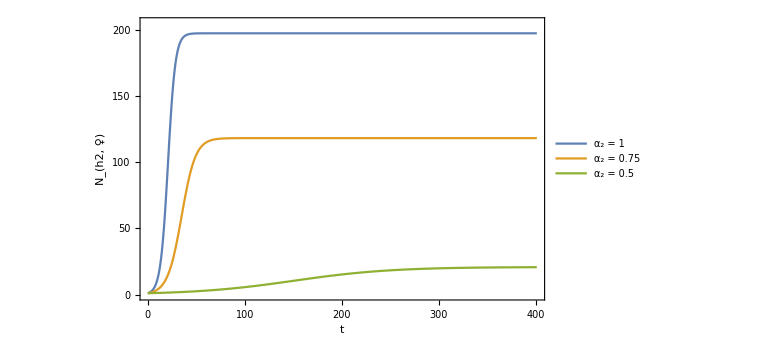

```mathematica
Plot[{Evaluate[yf[t]/.Dyn3],Evaluate[yf[t]/.Dyn2],Evaluate[yf[t]/.Dyn1]},{t,0,401},PlotRange->{{0,401},{0,205}},Frame->True,FrameStyle->Thick,FrameTicks->{{{0,50,100,150,200},None},{{0,100,200,300,400},None}},LabelStyle->Directive[Bold,18,Black],ImageSize->Large,FrameLabel->{"t","N_(h2, ♀)"},RotateLabel->False,PlotLegends->{"α_2 = 1","α_2 = 0.75","α_2 = 0.5"}]
```

```mathematica
Dyn1=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.1,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.1,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.1,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.1,xf[0]==156.2463535752091,xm[0]==156.2463535752091,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn2=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.5,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.5,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.5,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.5,xf[0]==156.2463535752091,xm[0]==156.2463535752091,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn3=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->1,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->1,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->1,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.85/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->1,xf[0]==156.2463535752091,xm[0]==156.2463535752091,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

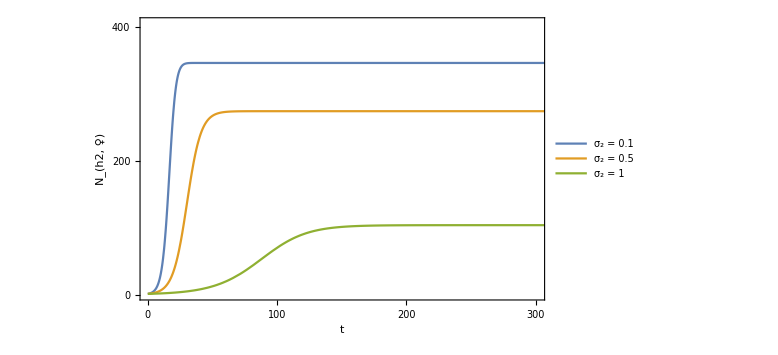

```mathematica
Plot[{Evaluate[yf[t]/.Dyn3],Evaluate[yf[t]/.Dyn2],Evaluate[yf[t]/.Dyn1]},{t,0,500},PlotRange->{{0,301},{0,405}},Frame->True,FrameStyle->Thick,FrameTicks->{{{0,200,400},None},{{0,100,200,300,400},None}},LabelStyle->Directive[Bold,18,Black],ImageSize->Large,FrameLabel->{"t","N_(h2, ♀)"},RotateLabel->False,PlotLegends->{"σ_2 = 0.1","σ_2 = 0.5","σ_2 = 1"}]
```

```mathematica
Dyn1=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0.1/.Subscript[σ, 2]->1,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0.1/.Subscript[σ, 2]->1,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0.1/.Subscript[σ, 2]->1,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0.1/.Subscript[σ, 2]->1,xf[0]==143.23251999213426,xm[0]==143.23251999213426,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn2=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0.5/.Subscript[σ, 2]->1,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1//.Subscript[α, 2]->1/.Subscript[β, 2]->0.5/.Subscript[σ, 2]->1,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0.5/.Subscript[σ, 2]->1,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->0.5/.Subscript[σ, 2]->1,xf[0]==143.23251999213426,xm[0]==143.23251999213426,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn3=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.5/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,xf[0]==143.23251999213426,xm[0]==143.23251999213426,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

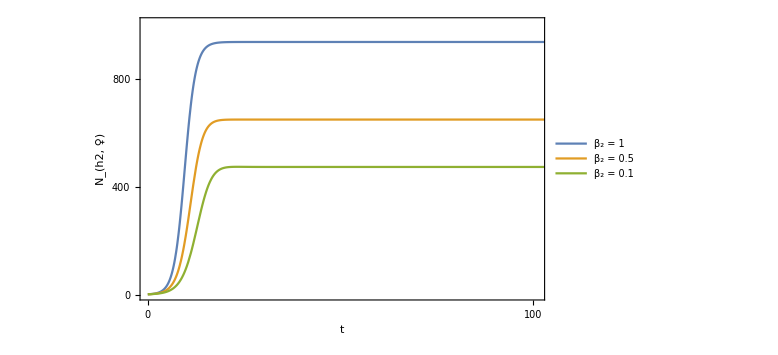

```mathematica
Plot[{Evaluate[yf[t]/.Dyn3],Evaluate[yf[t]/.Dyn2],Evaluate[yf[t]/.Dyn1]},{t,0,500},PlotRange->{{0,101},{0,1005}},Frame->True,FrameStyle->Thick,FrameTicks->{{{0,400,800},None},{{0,100,200,300,400},None}},LabelStyle->Directive[Bold,18,Black],ImageSize->Large,FrameLabel->{"t","N_(h2, ♀)"},RotateLabel->False,PlotLegends->{"β_2 = 1","β_2 = 0.5","β_2 = 0.1"}]
```

## Spread of alternative Mutants

Any mutant may spread if it has a larger birth rate than previously established mutants (see main text). The birth rate can serve as a fitness function:

```mathematica
w=(1+Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3])//FullSimplify;
```

To look for its maxima, we derive the partial derivatives of it :

```mathematica
D[w/.Subscript[β, 3] ->Subscript[β, 2]/.Subscript[σ, 3]->Subscript[σ, 2],Subscript[α, 3]]//FullSimplify
```

1/4 (1+σ_2) (-1-3 β_2 (-1+Φ_hh)+3 Φ_hh)

```mathematica
D[w/.Subscript[α, 3] ->Subscript[α, 2]/.Subscript[σ, 3]->Subscript[σ, 2],Subscript[β, 3]]//FullSimplify
```

-1/4 (-1+3 α_2) (1+σ_2) (-1+Φ_hh)

```mathematica
D[w/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[β, 3] ->Subscript[β, 2],Subscript[σ, 3]]//FullSimplify
```

1/4 ((-1+β_2) (-1+Φ_hh)+α_2 (-1-3 β_2 (-1+Φ_hh)+3 Φ_hh))

The sign of D[f/.β_3 ->β_2/.σ_3->σ_2,α_3] depends on the sign of (-1-3 β_2 (-1+Φ_hh)+3 Φ_hh).

Browsing parameter values, we show that (-1-3 β_2 (-1+Φ_hh)+3 Φ_hh) is never negative, such that the fitness function is maximized at α_3 = 1.

In the following: 
(1) we set values for α_2, β_2, σ_2, c_p and c_h, browsing the whole range of parameter values;
(2) we calculate numerically Φ_hh at the wt equilibrium for all parameter combinations; we proceed if Φ_hh > 1/3 - in the contrary, we know that gynogenesis cannot evolve;
(3) we calculate numerically α_lim; we will then only consider values of α greater than α_lim (in the contrary, again we know that asexuality cannot evolve);
(4) we calculate numerically the equilibria of the system, only consider the ones such that all population sizes are real and positive. We record in separate vectors whether there is no possible equilibrium, one possible equilibrium or several possible equilibria. The emptiness of MultiSol vectors prove that there never are more than one possible equilibrium for the system. There may be no equilibrium, but we see that it always correspond to values of σ_2 < 0, parameter values that we will see below should not occur.
(5) we calculate numerically (-1-3 β_2 (-1+Φ_hh)+3 Φ_hh);
(6) we write numerical values of (-1-3 β_2 (-1+Φ_hh)+3 Φ_hh) in an output data file, and record in a Mathematica vector any parameter combination such that it is negative; the emptiness of such vector proves that it is always positive

```mathematica
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Phi.csv",{},"Table"];
Α=Table[(i-1)/10.,{i,1,11}];
Β=Table[(j-1)/10.,{j,1,11}];
Σ=Table[(k-1)/10.-1/2,{k,1,11}];
CP=Table[(t)/10.,{t,1,9}];
CH=Table[(u)/10.,{u,1,9}];
SCAN={};
Vec1={};
Vec2={};
Vec3={};
NoSol={};
MultiSol={};
For[i=1,i≤11,i++,
For[j=1,j≤11,j++,
For[k=1,k≤11,k++,
For[t=1,t≤9,t++,
For[u=1,u≤9,u++,
Subscript[ϕ, 0]=Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[Subscript[ϕ, 0]>1/3,
Subscript[α, 0]=(-K+8 Subscript[N, h1]+K Subscript[Φ, hh])/(-K+3 K Subscript[Φ, hh])/.Subscript[N, h1]->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[Α[[i]]>=Subscript[α, 0],
NumbSol=0;
IdSol=0;
Nh = 0;
Sol=Solve[(Subscript[g, m]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&(Subscript[g, l] ==0/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})&&(g_(h1,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&(g_(h1,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&(g_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&(g_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->Β[[j]],Subscript[σ, 2]->Σ[[k]]})==0&&Subscript[N, m]≠0&&Subscript[N, l]≠0&&N_(h2,♀)≠0,{Subscript[N, m],Subscript[N, l],N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
For[n=1,n<=Length[Sol],++n,
If[(N_(h1,♂)/.Sol[[n]])∈Reals,
If[((N_(h1,♂)/.Sol[[n]])>0)&&((N_(h2,♂)/.Sol[[n]])>0),NumbSol=NumbSol+1;
IdSol=n]]];
If[NumbSol==0,AppendTo[NoSol,{Α[[i]],Β[[j]],Σ[[k]],CP[[t]],CH[[u]]}]];
If[NumbSol==1,Nh=(N_(h1,♂)/.Sol[[IdSol]])+(N_(h2,♂)/.Sol[[IdSol]]);
ϕ=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10;
str=OpenAppend["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Phi.csv"];
Write[str,-1-3 Β[[j]] (-1+ϕ)+3 ϕ];
Close[str];
If[-1-3 Β[[j]] (-1+ϕ)+3 ϕ≤0,AppendTo[SCAN,{Α[[i]],Β[[j]],Σ[[k]],CP[[t]],CH[[u]],ϕ}]];];
If[NumbSol>1,AppendTo[MultiSol,{Α[[i]],Β[[j]],Σ[[k]],CP[[t]],CH[[u]]}]]]]]]]]];
```

```mathematica
SCAN
```

{}

There is no numerical values of the parameters where (-1-3 β_2 (-1+Φ_hh)+3 Φ_hh) is negative.

In the following, we give some numerical example of (-1-3 β_2 (-1+Φ_hh)+3 Φ_hh):

β_2 = σ_2 = 0 / α_2 = 0.15 - 0.5 - 0.85

```mathematica
Α={0.15,0.5,0.85};
CP=Table[(t)/200.,{t,1,199}];
CH=Table[(u)/200.,{u,1,199}];
SCAN={};
Vec={};
For[i=1,i≤3,i++,
Print[i];
VEC={};
For[t=1,t≤199,t++,
For[u=1,u≤199,u++,
Subscript[ϕ, 0]=Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[Subscript[ϕ, 0]>1/3,
Subscript[α, 0]=(-K+8 Subscript[N, h1]+K Subscript[Φ, hh])/(-K+3 K Subscript[Φ, hh])/.Subscript[N, h1]->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[Α[[i]]>=Subscript[α, 0],
Sol=Solve[(Subscript[f, m]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->0,Subscript[σ, 2]->0})==0&&(Subscript[f, l] ==0/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->0,Subscript[σ, 2]->0})&&(f_(h1,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->0,Subscript[σ, 2]->0})==0&&(f_(h1,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->0,Subscript[σ, 2]->0})==0&&(f_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->0,Subscript[σ, 2]->0})==0&&(f_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->Α[[i]],Subscript[β, 2]->0,Subscript[σ, 2]->0})==0&&Subscript[N, m]≠0&&Subscript[N, l]≠0&&N_(h2,♀)≠0,{Subscript[N, m],Subscript[N, l],N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=0;
IdSol=0;
For[n=1,n<=Length[Sol],++n,
If[(N_(h1,♂)/.Sol[[n]])∈Reals,
If[((N_(h1,♀)/.Sol[[n]])>=0)&&((N_(h2,♀)/.Sol[[n]])>=0)&&((N_(h1,♂)/.Sol[[n]])>=0)&&((N_(h2,♂)/.Sol[[n]])>=0),NumbSol=NumbSol+1;
IdSol=n]]];
If[NumbSol==0,Print["ERROR: No possible equilibrium"];Print[Sol]];
If[NumbSol==1,Nh=(N_(h1,♂)/.Sol[[IdSol]])+(N_(h2,♂)/.Sol[[IdSol]]);
ϕ=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10;
AppendTo[VEC,{CH[[u]],CP[[t]],-1-3 Subscript[β, 2] (-1+ϕ)+3 ϕ/.Subscript[β, 2] ->0}]];
If[NumbSol>1,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]];]]]];
AppendTo[Vec,VEC]];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_a1.txt",Vec[[1]],"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_a2.txt",Vec[[2]],"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_a3.txt",Vec[[3]],"Table"];
VVec1=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_a1.txt","Table"];
VVec2=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_a2.txt","Table"];
VVec3=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_a3.txt","Table"];
```

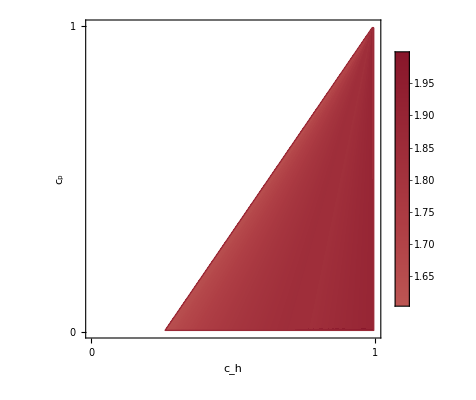

```mathematica
ListDensityPlot[VVec1,PlotRange->{{0,1},{0,1}},PlotLegends->Automatic,FrameLabel->{"c_h","c_p"},RotateLabel->False, BoundaryStyle->Directive[Lighter[Black],Thick],FrameTicks->{{{0,1},None},{{0,1},None}},FrameStyle->Directive[Black,Thick],PlotLegends->BarLegend[{Automatic,{-1,2}},20],ColorFunction->ColorData[{"ThermometerColors",{-1,2}}],ColorFunctionScaling->False,LabelStyle->16]
```

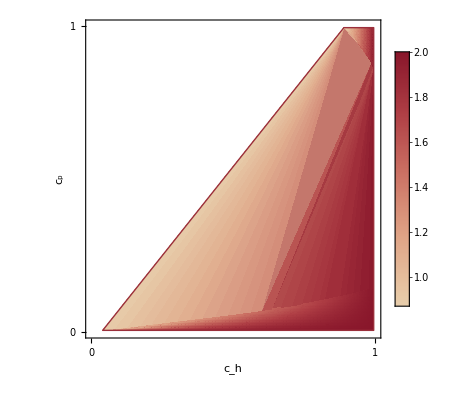

```mathematica
ListDensityPlot[VVec2,PlotRange->{{0,1},{0,1}},PlotLegends->Automatic,FrameLabel->{"c_h","c_p"},RotateLabel->False, BoundaryStyle->Directive[Lighter[Black],Thick],FrameTicks->{{{0,1},None},{{0,1},None}},FrameStyle->Directive[Black,Thick],PlotLegends->BarLegend[{Automatic,{-1,2}},20],ColorFunction->ColorData[{"ThermometerColors",{-1,2}}],ColorFunctionScaling->False,LabelStyle->16]
```

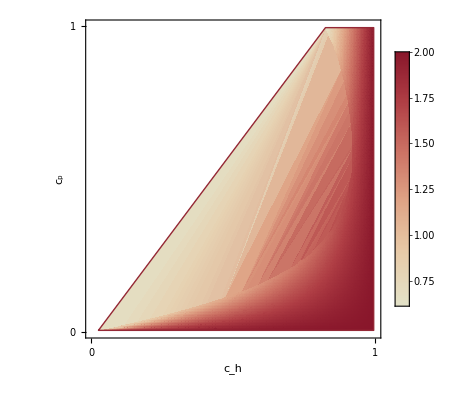

```mathematica
ListDensityPlot[VVec3,PlotRange->{{0,1},{0,1}},PlotLegends->Automatic,FrameLabel->{"c_h","c_p"},RotateLabel->False, BoundaryStyle->Directive[Lighter[Black],Thick],FrameTicks->{{{0,1},None},{{0,1},None}},FrameStyle->Directive[Black,Thick],PlotLegends->BarLegend[{Automatic,{-1,2}},20],ColorFunction->ColorData[{"ThermometerColors",{-1,2}}],ColorFunctionScaling->False,LabelStyle->16]
```

α_2 = 1 / β_2 = 0 / σ_2 = 0.0 - 0.5 - 0.1

```mathematica
Σ={0.0,0.5,1};
CP=Table[(t)/200.,{t,1,199}];
CH=Table[(u)/200.,{u,1,199}];
SCAN={};
Vec2={};
For[i=1,i≤3,i++,
Print[i];
VEC2={};
For[t=1,t≤199,t++,
For[u=1,u≤199,u++,
Subscript[ϕ, 0]=Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[Subscript[ϕ, 0]>1/3,
Subscript[α, 0]=(-K+8 Subscript[N, h1]+K Subscript[Φ, hh])/(-K+3 K Subscript[Φ, hh])/.Subscript[N, h1]->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[1>=Subscript[α, 0],
Sol=Solve[(Subscript[f, m]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->0,Subscript[σ, 2]->Σ[[i]]})==0&&(Subscript[f, l] ==0/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->0,Subscript[σ, 2]->Σ[[i]]})&&(f_(h1,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->0,Subscript[σ, 2]->Σ[[i]]})==0&&(f_(h1,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->0,Subscript[σ, 2]->Σ[[i]]})==0&&(f_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->0,Subscript[σ, 2]->Σ[[i]]})==0&&(f_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->0,Subscript[σ, 2]->Σ[[i]]})==0&&Subscript[N, m]≠0&&Subscript[N, l]≠0&&N_(h2,♀)≠0,{Subscript[N, m],Subscript[N, l],N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=0;
IdSol=0;
For[n=1,n<=Length[Sol],++n,
If[(N_(h1,♂)/.Sol[[n]])∈Reals,
If[((N_(h1,♀)/.Sol[[n]])>=0)&&((N_(h2,♀)/.Sol[[n]])>=0)&&((N_(h1,♂)/.Sol[[n]])>=0)&&((N_(h2,♂)/.Sol[[n]])>=0),NumbSol=NumbSol+1;
IdSol=n]]];
If[NumbSol==0,Print["ERROR: No possible equilibrium"];Print[Sol]];
If[NumbSol==1,Nh=(N_(h1,♂)/.Sol[[IdSol]])+(N_(h2,♂)/.Sol[[IdSol]]);
ϕ=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10;
AppendTo[VEC2,{CH[[u]],CP[[t]],-1-3 Subscript[β, 2] (-1+ϕ)+3 ϕ/.Subscript[β, 2] ->0}]];
If[NumbSol>1,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]];]]]];
AppendTo[Vec2,VEC2]];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_s1.txt",Vec2[[1]],"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_s2.txt",Vec2[[2]],"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_s3.txt",Vec2[[3]],"Table"];
VVec21=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_s1.txt","Table"];
VVec22=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_s2.txt","Table"];
VVec23=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_s3.txt","Table"];
```

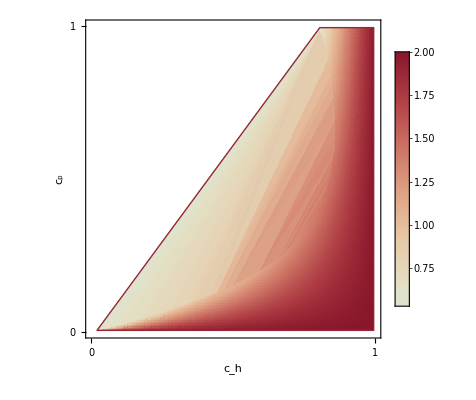

```mathematica
ListDensityPlot[VVec21,PlotRange->{{0,1},{0,1}},PlotLegends->Automatic,FrameLabel->{"c_h","c_p"},RotateLabel->False, BoundaryStyle->Directive[Lighter[Black],Thick],FrameTicks->{{{0,1},None},{{0,1},None}},FrameStyle->Directive[Black,Thick],PlotLegends->BarLegend[{Automatic,{-1,2}},20],ColorFunction->ColorData[{"ThermometerColors",{-1,2}}],ColorFunctionScaling->False,LabelStyle->16]
```

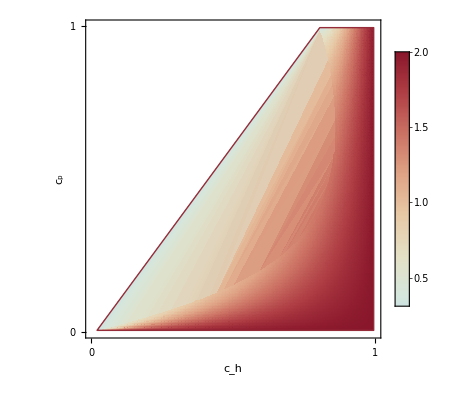

```mathematica
ListDensityPlot[VVec22,PlotRange->{{0,1},{0,1}},PlotLegends->Automatic,FrameLabel->{"c_h","c_p"},RotateLabel->False, BoundaryStyle->Directive[Lighter[Black],Thick],FrameTicks->{{{0,1},None},{{0,1},None}},FrameStyle->Directive[Black,Thick],PlotLegends->BarLegend[{Automatic,{-1,2}},20],ColorFunction->ColorData[{"ThermometerColors",{-1,2}}],ColorFunctionScaling->False,LabelStyle->16]
```

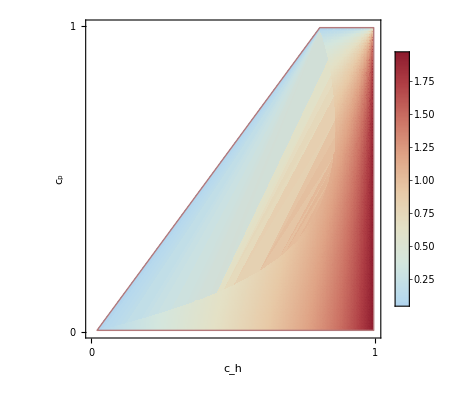

```mathematica
ListDensityPlot[VVec23,PlotRange->{{0,1},{0,1}},PlotLegends->Automatic,FrameLabel->{"c_h","c_p"},RotateLabel->False, BoundaryStyle->Directive[Lighter[Black],Thick],FrameTicks->{{{0,1},None},{{0,1},None}},FrameStyle->Directive[Black,Thick],PlotLegends->BarLegend[{Automatic,{-1,2}},20],ColorFunction->ColorData[{"ThermometerColors",{-1,2}}],ColorFunctionScaling->False,LabelStyle->16]
```

α_2 = σ_2 = 1 / β_2 = 0.1 - 0.5 - 0.1

```mathematica
Β={0.1,0.5,1};
CP=Table[(t)/200.,{t,1,199}];
CH=Table[(u)/200.,{u,1,199}];
SCAN={};
Vec3={};
For[i=1,i≤3,i++,
VEC3={};
For[t=1,t≤199,t++,
For[u=1,u≤199,u++,
Subscript[ϕ, 0]=Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[Subscript[ϕ, 0]>1/3,
Subscript[α, 0]=(-K+8 Subscript[N, h1]+K Subscript[Φ, hh])/(-K+3 K Subscript[Φ, hh])/.Subscript[N, h1]->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]};
If[1>=Subscript[α, 0],
Sol=Solve[(Subscript[f, m]/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->Β[[i]],Subscript[σ, 2]->1})==0&&(Subscript[f, l] ==0/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->Β[[i]],Subscript[σ, 2]->1})&&(f_(h1,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->Β[[i]],Subscript[σ, 2]->1})==0&&(f_(h1,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->Β[[i]],Subscript[σ, 2]->1})==0&&(f_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->Β[[i]],Subscript[σ, 2]->1})==0&&(f_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10/.{Subscript[α, 2]->1,Subscript[β, 2]->Β[[i]],Subscript[σ, 2]->1})==0&&Subscript[N, m]≠0&&Subscript[N, l]≠0&&N_(h2,♀)≠0,{Subscript[N, m],Subscript[N, l],N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=0;
IdSol=0;
For[n=1,n<=Length[Sol],++n,
If[(N_(h1,♂)/.Sol[[n]])∈Reals,
If[((N_(h1,♀)/.Sol[[n]])>=0)&&((N_(h2,♀)/.Sol[[n]])>=0)&&((N_(h1,♂)/.Sol[[n]])>=0)&&((N_(h2,♂)/.Sol[[n]])>=0),NumbSol=NumbSol+1;
IdSol=n]]];
If[NumbSol==0,Print["ERROR: No possible equilibrium"];Print[Sol]];
If[NumbSol==1,Nh=(N_(h1,♂)/.Sol[[IdSol]])+(N_(h2,♂)/.Sol[[IdSol]]);
ϕ=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[t]],Subscript[c, h]->CH[[u]]}/.K->10;
AppendTo[VEC3,{CH[[u]],CP[[t]],-1-3 Subscript[β, 2] (-1+ϕ)+3 ϕ/.Subscript[β, 2] ->Β[[i]]}]];
If[NumbSol>1,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]];]]]];
AppendTo[Vec3,VEC3]];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_b1.txt",Vec3[[1]],"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_b2.txt",Vec3[[2]],"Table"];
Export["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_b3.txt",Vec3[[3]],"Table"];
VVec31=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_b1.txt","Table"];
VVec32=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_b2.txt","Table"];
VVec33=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\AmazonMolly\\Genetic Models\\Density Models (4th gen)\\Pos_b3.txt","Table"];
```

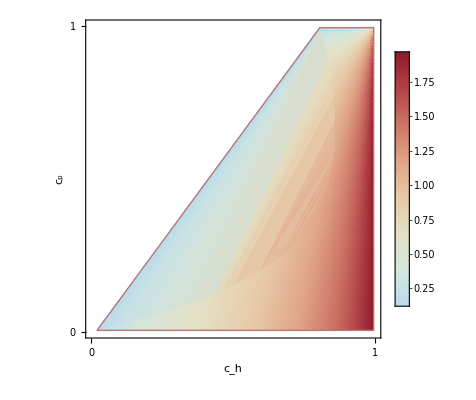

```mathematica
ListDensityPlot[VVec31,PlotRange->{{0,1},{0,1}},PlotLegends->Automatic,FrameLabel->{"c_h","c_p"},RotateLabel->False, BoundaryStyle->Directive[Lighter[Black],Thick],FrameTicks->{{{0,1},None},{{0,1},None}},FrameStyle->Directive[Black,Thick],PlotLegends->BarLegend[{Automatic,{-1,2}},20],ColorFunction->ColorData[{"ThermometerColors",{-1,2}}],ColorFunctionScaling->False,LabelStyle->16]
```

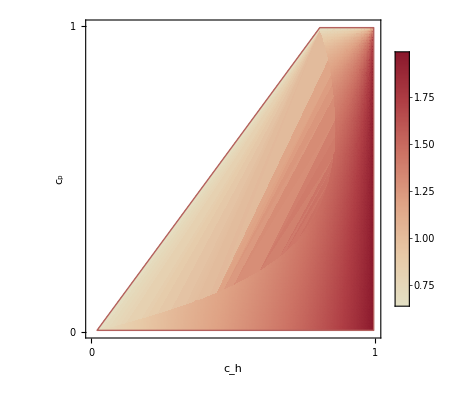

```mathematica
ListDensityPlot[VVec32,PlotRange->{{0,1},{0,1}},PlotLegends->Automatic,FrameLabel->{"c_h","c_p"},RotateLabel->False, BoundaryStyle->Directive[Lighter[Black],Thick],FrameTicks->{{{0,1},None},{{0,1},None}},FrameStyle->Directive[Black,Thick],PlotLegends->BarLegend[{Automatic,{-1,2}},20],ColorFunction->ColorData[{"ThermometerColors",{-1,2}}],ColorFunctionScaling->False,LabelStyle->16]
```

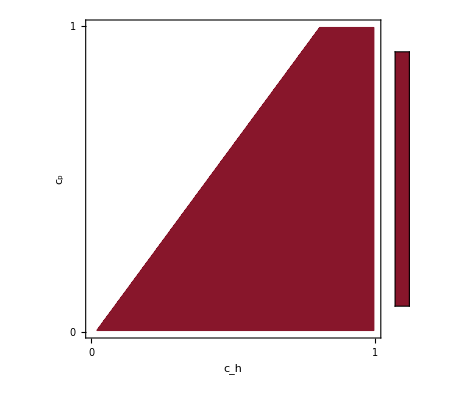

```mathematica
ListDensityPlot[VVec33,PlotRange->{{0,1},{0,1}},PlotLegends->Automatic,FrameLabel->{"c_h","c_p"},RotateLabel->False, BoundaryStyle->Directive[Lighter[Black],Thick],FrameTicks->{{{0,1},None},{{0,1},None}},FrameStyle->Directive[Black,Thick],PlotLegends->BarLegend[{Automatic,{-1,2}},20],ColorFunction->ColorData[{"ThermometerColors",{-1,2}}],ColorFunctionScaling->False,LabelStyle->16]
```

## Evolutionary Routes

To determine which evolutionary route should gynogenesis take, we compare the derivatives of the fitness function and assume that at any time, the next mutation to spread will be the one with the highest fitness derivative.

### c_p = 0.1

```mathematica
CP=0.1;
CH={0.4,0.5,0.9};
ω=Table[{0,0,0},{j,1,3},{i,1,1000}];
For[j=1,j<4,++j,
Subscript[α, 0]=(-K+8 Subscript[N, h1]+K Subscript[Φ, hh])/(-K+3 K Subscript[Φ, hh])/.Subscript[N, h1]->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]};
If[Subscript[α, 0]<=0,Subscript[α, 0]=0;,
If[Subscript[α, 0]<1,
ω[[j]][[2]]={Subscript[α, 0]+0.001,0,0};
ϕ=Table[0,{i,1,1000}];
g=((1+Subscript[ϵ, 3])/2)((((1-Subscript[α, 3])(1-Subscript[β, 3]))/2)(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3]);
D1=D[g/.Subscript[β, 3] ->Subscript[β, 2]/.Subscript[ϵ, 3]->Subscript[σ, 2],Subscript[α, 3]];
D2=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[ϵ, 3]->Subscript[σ, 2],Subscript[β, 3]];
D3=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[β, 3]->Subscript[β, 2],Subscript[ϵ, 3]];
For[i=2,i<1000,i++,
Nh = 0;
Sol=Solve[(((1/2)Subscript[Φ, mm]-Subscript[Ψ, m])Subscript[N, m]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&( ((1/2)Subscript[Φ, ll]-Subscript[Ψ, l])Subscript[N, l]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((Subscript[Φ, ml] Subscript[N, m])/2 + (Subscript[Φ, lm] Subscript[N, l])/2+((1-Subscript[Φ, hh])/2-Subscript[Ψ, h])N_(h1,♀)+((1+Subscript[σ, 2])/4)(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((Subscript[Φ, ml] Subscript[N, m] )/2+ (Subscript[Φ, lm] Subscript[N, l])/2+(((1-Subscript[Φ, hh])/2)N_(h1,♀)-Subscript[Ψ, h] N_(h1,♂))+((1-Subscript[σ, 2])/4)(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((((1+Subscript[σ, 2])/2)((((1-Subscript[α, 2])(1-Subscript[β, 2]))/2)(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-Subscript[Ψ, h])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&(((1-Subscript[σ, 2])/2)((((1-Subscript[α, 2])(1-Subscript[β, 2]))/2)(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&Subscript[N, m]≠0&&Subscript[N, l]≠0&&N_(h2,♀)≠0,{Subscript[N, m],Subscript[N, l],N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=0;
IdSol=0;
For[k=1,k<=Length[Sol],++k,
If[(N_(h1,♂)/.Sol[[k]])∈Reals,
If[((N_(h1,♀)/.Sol[[k]])>=0)&&((N_(h2,♀)/.Sol[[k]])>=0)&&((N_(h1,♂)/.Sol[[k]])>=0)&&((N_(h2,♂)/.Sol[[k]])>=0),NumbSol=NumbSol+1;
IdSol=k]]];
If[NumbSol==0,Print["ERROR: No possible equilibrium"];Print[Sol]];
If[NumbSol==1,Nh=(N_(h1,♂)/.Sol[[IdSol]])+(N_(h2,♂)/.Sol[[IdSol]]);
ϕ[[i]]=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10;
If[ω[[j]][[i]][[1]]<1,Direc1=D1/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc1=0];
If[ω[[j]][[i]][[2]]<1,Direc2=D2/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc2=0];
If[ω[[j]][[i]][[3]]<1,Direc3=D3/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc3=0];
Direc=Max[Abs[Direc1],Abs[Direc2],Abs[Direc3]];
υ=1/100;
If[Direc==Abs[Direc1],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc2],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]]+υ*Sign[Direc2];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc3],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]+υ*Sign[Direc3]];
If[ω[[j]][[i+1]][[1]]>1,ω[[j]][[i+1]][[1]]=1];
If[ω[[j]][[i+1]][[1]]<0,ω[[j]][[i+1]][[1]]=0];
If[ω[[j]][[i+1]][[2]]>1,ω[[j]][[i+1]][[2]]=1];
If[ω[[j]][[i+1]][[2]]<0,ω[[j]][[i+1]][[2]]=0];
If[ω[[j]][[i+1]][[3]]>1,ω[[j]][[i+1]][[3]]=1];
If[ω[[j]][[i+1]][[3]]<-1,ω[[j]][[i+1]][[3]]=-1];
,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]]]]]];
Plot3=ListPointPlot3D[{ω[[1]],ω[[2]],ω[[3]]},AxesLabel->{"α","β","σ"},PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[PointSize[0.007],Opacity[0.8]],LabelStyle->Directive[Black,Bold],ImageSize->Large,PlotLegends->{"c_h = 0.4","c_h = 0.5","c_h = 0.9"},PlotLabel->"c_p = 0.1"];
```

Transforming that into a 2 D space with the size of the points taking into account the α dimension :

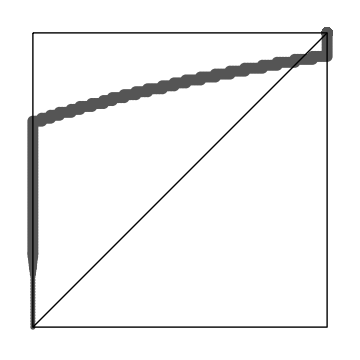

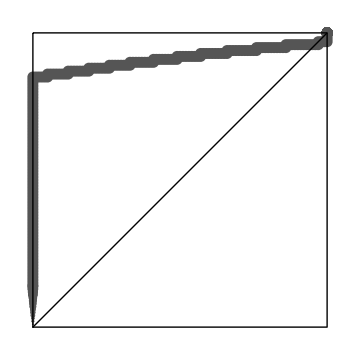

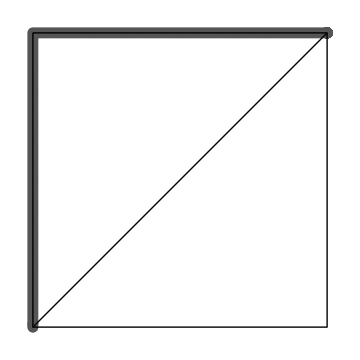

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[1]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[2]]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[3]]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```

### c_p = 0.5

```mathematica
CP=0.5;
CH={0.88,0.94,0.99};
ω=Table[{0,0,0},{j,1,3},{i,1,1000}];
For[j=1,j<4,++j,
Subscript[α, 0]=(-K+8 Subscript[N, h1]+K Subscript[Φ, hh])/(-K+3 K Subscript[Φ, hh])/.Subscript[N, h1]->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]};
If[Subscript[α, 0]<=0,Subscript[α, 0]=0;,
If[Subscript[α, 0]<1,
ω[[j]][[2]]={Subscript[α, 0]+0.001,0,0};
ϕ=Table[0,{i,1,1000}];
g=((1+Subscript[ϵ, 3])/2)((((1-Subscript[α, 3])(1-Subscript[β, 3]))/2)(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3]);
D1=D[g/.Subscript[β, 3] ->Subscript[β, 2]/.Subscript[ϵ, 3]->Subscript[σ, 2],Subscript[α, 3]];
D2=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[ϵ, 3]->Subscript[σ, 2],Subscript[β, 3]];
D3=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[β, 3]->Subscript[β, 2],Subscript[ϵ, 3]];
For[i=2,i<1000,i++,
Nh = 0;
Sol=Solve[(((1/2)Subscript[Φ, mm]-Subscript[Ψ, m])Subscript[N, m]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&( ((1/2)Subscript[Φ, ll]-Subscript[Ψ, l])Subscript[N, l]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((Subscript[Φ, ml] Subscript[N, m])/2 + (Subscript[Φ, lm] Subscript[N, l])/2+((1-Subscript[Φ, hh])/2-Subscript[Ψ, h])N_(h1,♀)+((1+Subscript[σ, 2])/4)(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((Subscript[Φ, ml] Subscript[N, m] )/2+ (Subscript[Φ, lm] Subscript[N, l])/2+(((1-Subscript[Φ, hh])/2)N_(h1,♀)-Subscript[Ψ, h] N_(h1,♂))+((1-Subscript[σ, 2])/4)(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((((1+Subscript[σ, 2])/2)((((1-Subscript[α, 2])(1-Subscript[β, 2]))/2)(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-Subscript[Ψ, h])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&(((1-Subscript[σ, 2])/2)((((1-Subscript[α, 2])(1-Subscript[β, 2]))/2)(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&Subscript[N, m]≠0&&Subscript[N, l]≠0&&N_(h2,♀)≠0,{Subscript[N, m],Subscript[N, l],N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=0;
IdSol=0;
For[k=1,k<=Length[Sol],++k,
If[(N_(h1,♂)/.Sol[[k]])∈Reals,
If[((N_(h1,♀)/.Sol[[k]])>=0)&&((N_(h2,♀)/.Sol[[k]])>=0)&&((N_(h1,♂)/.Sol[[k]])>=0)&&((N_(h2,♂)/.Sol[[k]])>=0),NumbSol=NumbSol+1;
IdSol=k]]];
If[NumbSol==0,Print["ERROR: No possible equilibrium"];Print[Sol]];
If[NumbSol==1,Nh=(N_(h1,♂)/.Sol[[IdSol]])+(N_(h2,♂)/.Sol[[IdSol]]);
ϕ[[i]]=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10;
If[ω[[j]][[i]][[1]]<1,Direc1=D1/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc1=0];
If[ω[[j]][[i]][[2]]<1,Direc2=D2/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc2=0];
If[ω[[j]][[i]][[3]]<1,Direc3=D3/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc3=0];
Direc=Max[Abs[Direc1],Abs[Direc2],Abs[Direc3]];
υ=1/100;
If[Direc==Abs[Direc1],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc2],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]]+υ*Sign[Direc2];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc3],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]+υ*Sign[Direc3]];
If[ω[[j]][[i+1]][[1]]>1,ω[[j]][[i+1]][[1]]=1];
If[ω[[j]][[i+1]][[1]]<0,ω[[j]][[i+1]][[1]]=0];
If[ω[[j]][[i+1]][[2]]>1,ω[[j]][[i+1]][[2]]=1];
If[ω[[j]][[i+1]][[2]]<0,ω[[j]][[i+1]][[2]]=0];
If[ω[[j]][[i+1]][[3]]>1,ω[[j]][[i+1]][[3]]=1];
If[ω[[j]][[i+1]][[3]]<-1,ω[[j]][[i+1]][[3]]=-1];
,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]]]]]];
Plot3=ListPointPlot3D[{ω[[1]],ω[[2]],ω[[3]]},AxesLabel->{"α","β","ϵ"},PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[PointSize[0.007],Opacity[0.8]],LabelStyle->Directive[Black,Bold],ImageSize->Large,PlotLegends->{"c_h = 0.4","c_h = 0.5","c_h = 0.9"},PlotLabel->"c_p = 0.5"];
```

Transforming that into a 2 D space with the size of the points taking into account the α dimension :

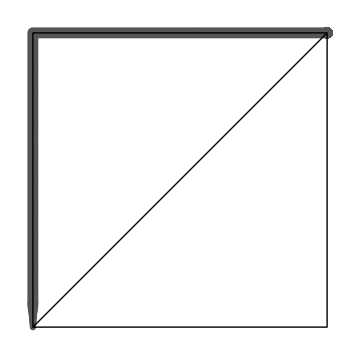

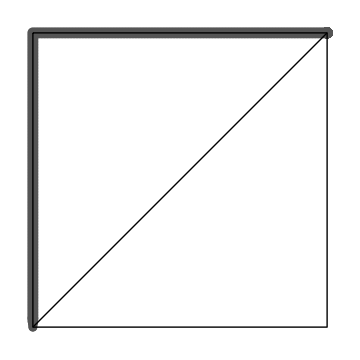

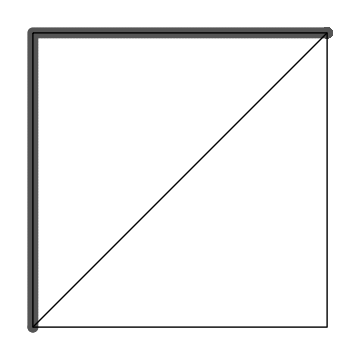

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[1]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[2]]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[3]]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```

### c_p = 0.9

```mathematica
CP=0.9;
CH={0.88,0.94,0.99};
ω=Table[{0,0,0},{j,1,3},{i,1,1000}];
For[j=1,j<4,++j,
Subscript[α, 0]=(-K+8 Subscript[N, h1]+K Subscript[Φ, hh])/(-K+3 K Subscript[Φ, hh])/.Subscript[N, h1]->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]};
If[Subscript[α, 0]<=0,Subscript[α, 0]=0;,
If[Subscript[α, 0]<1,
ω[[j]][[2]]={Subscript[α, 0]+0.001,0,0};
ϕ=Table[0,{i,1,1000}];
g=((1+Subscript[ϵ, 3])/2)((((1-Subscript[α, 3])(1-Subscript[β, 3]))/2)(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3]);
D1=D[g/.Subscript[β, 3] ->Subscript[β, 2]/.Subscript[ϵ, 3]->Subscript[σ, 2],Subscript[α, 3]];
D2=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[ϵ, 3]->Subscript[σ, 2],Subscript[β, 3]];
D3=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[β, 3]->Subscript[β, 2],Subscript[ϵ, 3]];
For[i=2,i<1000,i++,
Nh = 0;
Sol=Solve[(((1/2)Subscript[Φ, mm]-Subscript[Ψ, m])Subscript[N, m]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&( ((1/2)Subscript[Φ, ll]-Subscript[Ψ, l])Subscript[N, l]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((Subscript[Φ, ml] Subscript[N, m])/2 + (Subscript[Φ, lm] Subscript[N, l])/2+((1-Subscript[Φ, hh])/2-Subscript[Ψ, h])N_(h1,♀)+((1+Subscript[σ, 2])/4)(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((Subscript[Φ, ml] Subscript[N, m] )/2+ (Subscript[Φ, lm] Subscript[N, l])/2+(((1-Subscript[Φ, hh])/2)N_(h1,♀)-Subscript[Ψ, h] N_(h1,♂))+((1-Subscript[σ, 2])/4)(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((((1+Subscript[σ, 2])/2)((((1-Subscript[α, 2])(1-Subscript[β, 2]))/2)(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-Subscript[Ψ, h])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&(((1-Subscript[σ, 2])/2)((((1-Subscript[α, 2])(1-Subscript[β, 2]))/2)(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&Subscript[N, m]≠0&&Subscript[N, l]≠0&&N_(h2,♀)≠0,{Subscript[N, m],Subscript[N, l],N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=0;
IdSol=0;
For[k=1,k<=Length[Sol],++k,
If[(N_(h1,♂)/.Sol[[k]])∈Reals,
If[((N_(h1,♀)/.Sol[[k]])>=0)&&((N_(h2,♀)/.Sol[[k]])>=0)&&((N_(h1,♂)/.Sol[[k]])>=0)&&((N_(h2,♂)/.Sol[[k]])>=0),NumbSol=NumbSol+1;
IdSol=k]]];
If[NumbSol==0,Print["ERROR: No possible equilibrium"];Print[Sol]];
If[NumbSol==1,Nh=(N_(h1,♂)/.Sol[[IdSol]])+(N_(h2,♂)/.Sol[[IdSol]]);
ϕ[[i]]=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10;
If[ω[[j]][[i]][[1]]<1,Direc1=D1/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc1=0];
If[ω[[j]][[i]][[2]]<1,Direc2=D2/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc2=0];
If[ω[[j]][[i]][[3]]<1,Direc3=D3/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc3=0];
Direc=Max[Abs[Direc1],Abs[Direc2],Abs[Direc3]];
υ=1/100;
If[Direc==Abs[Direc1],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc2],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]]+υ*Sign[Direc2];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc3],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]+υ*Sign[Direc3]];
If[ω[[j]][[i+1]][[1]]>1,ω[[j]][[i+1]][[1]]=1];
If[ω[[j]][[i+1]][[1]]<0,ω[[j]][[i+1]][[1]]=0];
If[ω[[j]][[i+1]][[2]]>1,ω[[j]][[i+1]][[2]]=1];
If[ω[[j]][[i+1]][[2]]<0,ω[[j]][[i+1]][[2]]=0];
If[ω[[j]][[i+1]][[3]]>1,ω[[j]][[i+1]][[3]]=1];
If[ω[[j]][[i+1]][[3]]<-1,ω[[j]][[i+1]][[3]]=-1];
,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]]]]]];
Plot3=ListPointPlot3D[{ω[[1]],ω[[2]],ω[[3]]},AxesLabel->{"α","β","ϵ"},PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[PointSize[0.007],Opacity[0.8]],LabelStyle->Directive[Black,Bold],ImageSize->Large,PlotLegends->{"c_h = 0.4","c_h = 0.5","c_h = 0.9"},PlotLabel->"c_p = 0.9"];
```

Transforming that into a 2D space with the size of the points taking into account the α dimension:

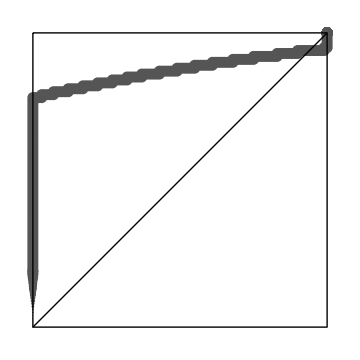

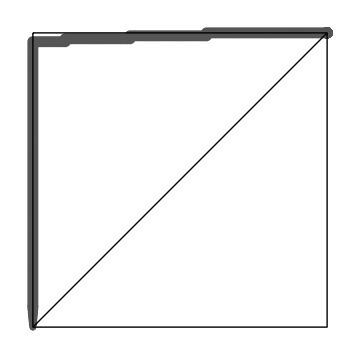

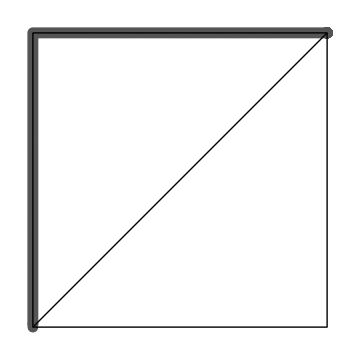

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[1]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[2]]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[3]]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```

## Population Sizes during Multiple invasions

We present in the following an example of multiple invasions of ever more asexual mutants. Throughout, we assume: K = 1000, c_p = 0.9, and c_h = 0.9. We start with the initial spread of wild-type mutants, and, after the first 100 generations, introduce new mutants every 400 generations.

```mathematica
Dyn1=NDSolve[{D[x[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(x[t]+x[t])/K)x[t]/.Subscript[Φ, hh]->(Subscript[c, h](x[t]))/(Subscript[c, h](x[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9,x[0]==1},x,{t,1,100}];
```

```mathematica
Dyn2=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0,xf[100]==x[100]/.Dyn1[[1]],xm[100]==x[100]/.Dyn1[[1]],yf[100]==1,ym[100]==1},{xf,xm,yf,ym},{t,100,500}];
```

```mathematica
Dyn3=NDSolve[{D[x1f[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(x1f[t]+x1m[t]+x2f[t]+x2m[t]+x3f[t]+x3m[t])/K)x1f[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])x2f[t]+(1+Subscript[σ, 3])/4(1-Subscript[α, 3])(1-Subscript[β, 3])(1-Subscript[Φ, hh])x3f[t]/.Subscript[Φ, hh]->(Subscript[c, h](x1m[t]+x2m[t]+x3m[t]))/(Subscript[c, h](x1m[t]+x2m[t]+x3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0,D[x1m[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 x1f[t]-(x1f[t]+x1m[t]+x2f[t]+x2m[t]+x3f[t]+x3m[t])/K x1m[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])x2f[t]+(1-Subscript[σ, 3])/4(1-Subscript[α, 3])(1-Subscript[β, 3])(1-Subscript[Φ, hh])x3f[t]/.Subscript[Φ, hh]->(Subscript[c, h](x1m[t]+x2m[t]+x3m[t]))/(Subscript[c, h](x1m[t]+x2m[t]+x3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0,D[x2f[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(x1f[t]+x1m[t]+x2f[t]+x2m[t]+x3f[t]+x3m[t])/K)x2f[t]/.Subscript[Φ, hh]->(Subscript[c, h](x1m[t]+x2m[t]+x3m[t]))/(Subscript[c, h](x1m[t]+x2m[t]+x3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0,D[x2m[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])x2f[t]-(x1f[t]+x1m[t]+x2f[t]+x2m[t]+x3f[t]+x3m[t])/K x2m[t])/.Subscript[Φ, hh]->(Subscript[c, h](x1m[t]+x2m[t]+x3m[t]))/(Subscript[c, h](x1m[t]+x2m[t]+x3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0,D[x3f[t],t]==((1+Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3])-(x1f[t]+x1m[t]+x2f[t]+x2m[t]+x3f[t]+x3m[t])/K)x3f[t]/.Subscript[Φ, hh]->(Subscript[c, h](x1m[t]+x2m[t]+x3m[t]))/(Subscript[c, h](x1m[t]+x2m[t]+x3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0,D[x3m[t],t]==((1-Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3])x3f[t]-(x1f[t]+x1m[t]+x2f[t]+x2m[t]+x3f[t]+x3m[t])/K x3m[t])/.Subscript[Φ, hh]->(Subscript[c, h](x1m[t]+x2m[t]+x3m[t]))/(Subscript[c, h](x1m[t]+x2m[t]+x3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.8/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0,x1f[500]==xf[500]/.Dyn2[[1]],x1m[500]==xm[500]/.Dyn2[[1]],x2f[500]==yf[500]/.Dyn2[[1]],x2m[500]==ym[500]/.Dyn2[[1]],x3f[500]==1,x3m[500]==1},{x1f,x1m,x2f,x2m,x3f,x3m},{t,500,900}];
```

```mathematica
Dyn4=NDSolve[{D[xx1f[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xx1f[t]+xx1m[t]+xx2f[t]+xx2m[t]+xx3f[t]+xx3m[t])/K)xx1f[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])xx2f[t]+(1+Subscript[σ, 3])/4(1-Subscript[α, 3])(1-Subscript[β, 3])(1-Subscript[Φ, hh])xx3f[t]/.Subscript[Φ, hh]->(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t]))/(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0.3,D[xx1m[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xx1f[t]-(xx1f[t]+xx1m[t]+xx2f[t]+xx2m[t]+xx3f[t]+xx3m[t])/K xx1m[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])xx2f[t]+(1-Subscript[σ, 3])/4(1-Subscript[α, 3])(1-Subscript[β, 3])(1-Subscript[Φ, hh])xx3f[t]/.Subscript[Φ, hh]->(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t]))/(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0.3,D[xx2f[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xx1f[t]+xx1m[t]+xx2f[t]+xx2m[t]+xx3f[t]+xx3m[t])/K)xx2f[t]/.Subscript[Φ, hh]->(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t]))/(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0.3,D[xx2m[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])xx2f[t]-(xx1f[t]+xx1m[t]+xx2f[t]+xx2m[t]+xx3f[t]+xx3m[t])/K xx2m[t])/.Subscript[Φ, hh]->(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t]))/(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0.3,D[xx3f[t],t]==((1+Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3])-(xx1f[t]+xx1m[t]+xx2f[t]+xx2m[t]+xx3f[t]+xx3m[t])/K)xx3f[t]/.Subscript[Φ, hh]->(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t]))/(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0.3,D[xx3m[t],t]==((1-Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3])xx3f[t]-(xx1f[t]+xx1m[t]+xx2f[t]+xx2m[t]+xx3f[t]+xx3m[t])/K xx3m[t])/.Subscript[Φ, hh]->(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t]))/(Subscript[c, h](xx1m[t]+xx2m[t]+xx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.Subscript[α, 3]->1/.Subscript[β, 3]->0/.Subscript[σ, 3]->0.3,xx1f[900]==x1f[900]/.Dyn3[[1]],xx1m[900]==x1m[900]/.Dyn3[[1]],xx2f[900]==x3f[900]/.Dyn3[[1]],xx2m[900]==x3m[900]/.Dyn3[[1]],xx3f[900]==1,xx3m[900]==1},{xx1f,xx1m,xx2f,xx2m,xx3f,xx3m},{t,900,1300}];
```

```mathematica
Dyn5=NDSolve[{D[xxx1f[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xxx1f[t]+xxx1m[t]+xxx2f[t]+xxx2m[t]+xxx3f[t]+xxx3m[t])/K)xxx1f[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])xxx2f[t]+(1+Subscript[σ, 3])/4(1-Subscript[α, 3])(1-Subscript[β, 3])(1-Subscript[Φ, hh])xxx3f[t]/.Subscript[Φ, hh]->(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t]))/(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.3/.Subscript[α, 3]->1/.Subscript[β, 3]->0.6/.Subscript[σ, 3]->0.3,D[xxx1m[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xxx1f[t]-(xxx1f[t]+xxx1m[t]+xxx2f[t]+xxx2m[t]+xxx3f[t]+xxx3m[t])/K xxx1m[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])xxx2f[t]+(1-Subscript[σ, 3])/4(1-Subscript[α, 3])(1-Subscript[β, 3])(1-Subscript[Φ, hh])xxx3f[t]/.Subscript[Φ, hh]->(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t]))/(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.3/.Subscript[α, 3]->1/.Subscript[β, 3]->0.6/.Subscript[σ, 3]->0.3,D[xxx2f[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])-(xxx1f[t]+xxx1m[t]+xxx2f[t]+xxx2m[t]+xxx3f[t]+xxx3m[t])/K)xxx2f[t]/.Subscript[Φ, hh]->(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t]))/(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.3/.Subscript[α, 3]->1/.Subscript[β, 3]->0.6/.Subscript[σ, 3]->0.3,D[xxx2m[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2](1-Subscript[β, 2])Subscript[Φ, hh]+Subscript[α, 2] Subscript[β, 2])xxx2f[t]-(xxx1f[t]+xxx1m[t]+xxx2f[t]+xxx2m[t]+xxx3f[t]+xxx3m[t])/K xxx2m[t])/.Subscript[Φ, hh]->(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t]))/(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.3/.Subscript[α, 3]->1/.Subscript[β, 3]->0.6/.Subscript[σ, 3]->0.3,D[xxx3f[t],t]==((1+Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3])-(xxx1f[t]+xxx1m[t]+xxx2f[t]+xxx2m[t]+xxx3f[t]+xxx3m[t])/K)xxx3f[t]/.Subscript[Φ, hh]->(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t]))/(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.3/.Subscript[α, 3]->1/.Subscript[β, 3]->0.6/.Subscript[σ, 3]->0.3,D[xxx3m[t],t]==((1-Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3](1-Subscript[β, 3])Subscript[Φ, hh]+Subscript[α, 3] Subscript[β, 3])xxx3f[t]-(xxx1f[t]+xxx1m[t]+xxx2f[t]+xxx2m[t]+xxx3f[t]+xxx3m[t])/K xxx3m[t])/.Subscript[Φ, hh]->(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t]))/(Subscript[c, h](xxx1m[t]+xxx2m[t]+xxx3m[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.9/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->0/.Subscript[σ, 2]->0.3/.Subscript[α, 3]->1/.Subscript[β, 3]->0.6/.Subscript[σ, 3]->0.3,xxx1f[1300]==xx1f[1300]/.Dyn4[[1]],xxx1m[1300]==xx1m[1300]/.Dyn4[[1]],xxx2f[1300]==xx3f[1300]/.Dyn4[[1]],xxx2m[1300]==xx3m[1300]/.Dyn4[[1]],xxx3f[1300]==1,xxx3m[1300]==1},{xxx1f,xxx1m,xxx2f,xxx2m,xxx3f,xxx3m},{t,1300,1700}];
```

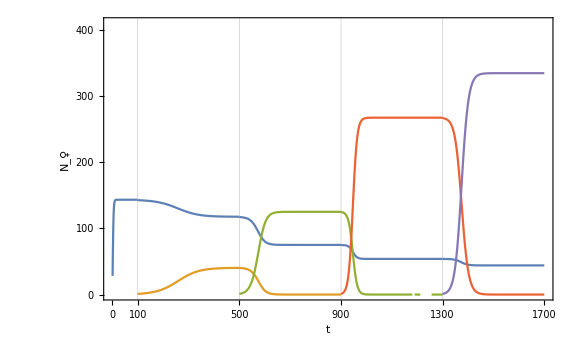

```mathematica
P1=Plot[Evaluate[x[t]/.Dyn1],{t,1,100},PlotRange->{{0,1700},{0,410}},GridLines->{{100,500,900,1300},None},Frame->True,FrameStyle->Thick,FrameTicks->{{{0,100,200,300,400},None},{{0,100,500,900,1300,1700},None}},LabelStyle->Directive[Bold,18,Black],ImageSize->Large,FrameLabel->{"t","N_♀"},RotateLabel->False];
P2=Plot[{Evaluate[xf[t]/.Dyn2],Evaluate[yf[t]/.Dyn2]},{t,100,500},PlotRange->{{0,1700},{0,500}}];
P3=Plot[{Evaluate[x1f[t]/.Dyn3],Evaluate[x2f[t]/.Dyn3],Evaluate[x3f[t]/.Dyn3]},{t,500,900},PlotRange->{{0,1700},{0,500}},GridLines->{{900},None}];
P4=Plot[{Evaluate[xx1f[t]/.Dyn4],Evaluate[xx2f[t]/.Dyn4],Evaluate[xx3f[t]/.Dyn4]},{t,900,1300},PlotRange->{{0,1700},{0,500}},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]}];
P5=Plot[{Evaluate[xxx1f[t]/.Dyn5],Evaluate[xxx2f[t]/.Dyn5],Evaluate[xxx3f[t]/.Dyn5]},{t,1300,1700},PlotRange->{{0,1700},{0,500}},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[5]]}];
Show[{P1,P2,P3,P4,P5}]
```

## Model 2: Egg Failure

## Dynamical Equations

g_i : growth function of population of class i.  6 classes in total: 
mex, lat, female wild-type hybrid, male wild-type hybrid, female mutant hybrid, male mutant hybrid.

```mathematica
g_(h1,♀)=(Subscript[Φ, ml] Subscript[N, m])/2 + (Subscript[Φ, lm] Subscript[N, l])/2+(0-Subscript[Ψ, h])N_(h1,♀);
g_(h1,♂)=(Subscript[Φ, ml] Subscript[N, m])/2+ (Subscript[Φ, lm] Subscript[N, l])/2+(0-Subscript[Ψ, h] N_(h1,♂));
g_(h2,♀)=((1+Subscript[σ, 2])/2 Subscript[α, 2]-Subscript[Ψ, h])N_(h2,♀);
g_(h2,♂)=((1-Subscript[σ, 2])/2 Subscript[α, 2])N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂);
```

## Wild - type hybrid initial equilibrium (wt)

### Equilibrium expression

We obtain the wild-type equilibrium in the absence of mutant hybrids by solving the ODEs assuming: (1) parents are at their equilibrium, (2) N_(h2,♀) = N_(h2,♂) = 0, and (3) N_(h1,♂) = N_(h1,♀) (because we assume that wild-type hybrids are entirely sexual and produced with unbiased sex-ratios.

```mathematica
Solve[(g_(h1,♀)/.N_(h2,♀)->0/.N_(h2,♂)->0/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.N_(h1,♂)->N_(h1,♀))==0&&K>0&&1>Subscript[c, p]>0&&1>Subscript[Φ, hh]>0&&N_(h1,♀)>0,{N_(h1,♀)},Reals]//FullSimplify
```

{{N_(h1,♀)→ConditionalExpression[(K √((1-c_p) c_p))/(2 √2), 0<Φ_hh<1&&K>0&&0<c_p<1]}}

### Equilibrium Stability

The stability of this equilibrium is determines by calculating the sign of (∂g_(h1,♀))/(∂N_(h1,♀)):

```mathematica
D[g_(h1,♀)/.N_(h2,♀)->0/.N_(h2,♂)->0/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.N_(h1,♂)->N_(h1,♀),N_(h1,♀)]/.N_(h1,♀)->(K √((1-Subscript[c, p]) Subscript[c, p]))/(2 √2)//FullSimplify
```

-√2 √(-(-1+c_p) c_p)

This is always negative : the equilibrium is stable.

## Conditions for the Spread of a Partial Apomictic Mutant h2 at wt equilibrium

### For any values of β and σ

```mathematica
Reduce[(((1+Subscript[σ, 2])/2 Subscript[α, 2]-Subscript[Ψ, h])/.N_(h2,♂)->0/.N_(h2,♀)->0/.N_(h1,♂)->N_(h1,♀)/.N_(h1,♀)->(K √((1-Subscript[c, p]) Subscript[c, p]))/(2 √2))>0&&N_(h1,♀)>0&&K>0&&1>Subscript[c, p]>0&&1≥Subscript[α, 2]≥0,Subscript[α, 2],Reals]//FullSimplify
```

K>0&&α_2≤1&&N_(h1,♀)>0&&((2 √(-(-1+c_p) c_p)<α_2&&1+σ_2==1/(√2)&&(0<c_p<1/2||1/2<c_p<1))||(√2 √(-((-1+c_p) c_p)/(1+σ_2)^2)<α_2&&((1+σ_2<1/(√2)&&1+σ_2>0&&((c_p<1&&1+√(-1-2 σ_2 (2+σ_2))<2 c_p)||(c_p>0&&2 c_p+√(-1-2 σ_2 (2+σ_2))<1)))||(0<c_p<1&&1+σ_2>1/(√2)))))

### For β = 0 and σ = 0

We prove in the main text that a first mutant h2 must be partially apomictic to have a chance to spread. We consider that the effect of the mutation is to only introduce some rate of apomixis. Such a mutant spreads if and only if g_(h2,♀)>0, which we prove in the main text may be possible only if Φ_hh>1/3:

```mathematica
Reduce[(((1+Subscript[σ, 2])/2 Subscript[α, 2]-Subscript[Ψ, h])/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.N_(h2,♂)->0/.N_(h2,♀)->0/.N_(h1,♂)->N_(h1,♀)/.N_(h1,♀)->(K √((1-Subscript[c, p]) Subscript[c, p]))/(2 √2))>0&&N_(h1,♀)>0&&K>0&&1>Subscript[c, p]>0&&1≥Subscript[α, 2]≥0,Subscript[α, 2],Reals]//FullSimplify
```

N_(h1,♀)>0&&K>0&&0<c_p<1&&√(2 c_p-2 c_p^2)<α_2≤1

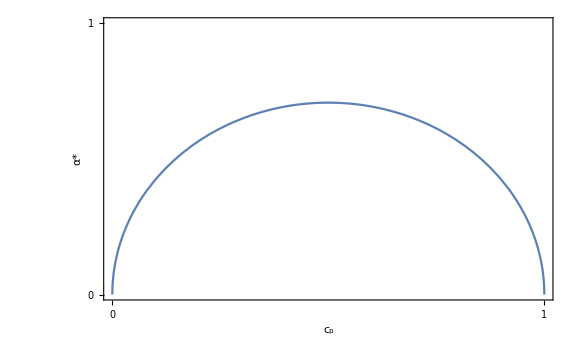

```mathematica
A1=Plot[{√(2 Subscript[c, p]-2 Subscript[c, p]^2)/.Subscript[c, h]->0.5/.K->10},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[1]],FrameStyle->Thick,FrameLabel->{"c_p","α*"},RotateLabel->False,ImageSize->Large,LabelStyle->Directive[20,Bold,Black],FrameTicks->{{{0,1},None},{{0,1},None}}]
```

## Wild - Type - Mutant Equilibrium

When the first apomictic mutant spreads, it can reach an equilibrium that we found by solving the ODEs assuming that (1) N_(h1,♂) = N_(h1,♀), and (2) N_(h2,♂) = N_(h2,♀).

```mathematica
Solve[(g_(h1,♀)/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.N_(h1,♂)->N_(h1,♀)/.N_(h2,♂)->N_(h2,♀))==0&&(g_(h2,♀)/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.Subscript[β, 2]->0/.Subscript[σ, 2]->0/.N_(h1,♂)->N_(h1,♀)/.N_(h2,♂)->N_(h2,♀))==0&&K>0&&1>Subscript[c, p]>0&&1>Subscript[Φ, hh]>1/3&&1≥Subscript[α, 2]≥0&&N_(h2,♀)≠0,{N_(h1,♀),N_(h2,♀)},Reals]//FullSimplify
```

{{N_(h1,♀)→ConditionalExpression[-(K (-1+c_p) c_p)/(2 α_2), ],N_(h2,♀)→ConditionalExpression[(K (2 (-1+c_p) c_p+α_2^2))/(4 α_2), ]}}

For σ_2 not equal to 0:

```mathematica
Reduce[(g_(h1,♀)/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.N_(h1,♂)->N_(h1,♀))==0&&(g_(h2,♀)/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.N_(h1,♂)->N_(h1,♀) )==0&&(g_(h1,♂)/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.N_(h1,♂)->N_(h1,♀) )==0&&(g_(h2,♂)/.Subscript[N, m]->(K Subscript[c, p])/4/.Subscript[N, l]->(K Subscript[c, p])/4/.N_(h1,♂)->N_(h1,♀) )==0&&K>0&&1>Subscript[c, p]>0&&1≥Subscript[α, 2]>√(2 Subscript[c, p]-2 Subscript[c, p]^2)&&1≥Subscript[σ, 2]≥-1&&N_(h1,♀)≠0&&N_(h2,♀)≠0,{N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)},Reals]//FullSimplify
```

(K (-1+c_p) c_p)/(α_2 (1+σ_2))+2 N_(h1,♀)==0&&(K^2 (-1+c_p) c_p)/(N_(h1,♀))+4 (2 N_(h1,♀)+N_(h2,♂)+N_(h2,♀))==0&&(K (-1+c_p) c_p (K^2 (-1+c_p) c_p+8 N_(h1,♀)^2))/(N_(h1,♀) (K (-1+c_p) c_p+2 α_2 (-1+σ_2) N_(h1,♀)))+4 N_(h2,♀)==0&&(-1<σ_2<-1+√2 √(-((-1+c_p) c_p)/α_2^2)||-1+√2 √(-((-1+c_p) c_p)/α_2^2)<σ_2≤1)&&0<c_p<1&&√(2 c_p-2 c_p^2)<α_2≤1&&K>0

N_(h1,♀)=-(K (-1+c_p) c_p)/(2 α_2 (1+σ_2))

```mathematica
(K (-1+Subscript[c, p]) Subscript[c, p] (K^2 (-1+Subscript[c, p]) Subscript[c, p]+8 N_(h1,♀)^2))/(N_(h1,♀) (K (-1+Subscript[c, p]) Subscript[c, p]+2 Subscript[α, 2] (-1+Subscript[σ, 2]) N_(h1,♀)))/.N_(h1,♀)->-(K (-1+Subscript[c, p]) Subscript[c, p])/(2 Subscript[α, 2] (1+Subscript[σ, 2]))//FullSimplify
```

-(2 K (-1+c_p) c_p)/α_2-K α_2 (1+σ_2)^2

N_(h2,♀)=(2 K (-1+c_p) c_p)/(4 α_2)+K α_2 (1+σ_2)^2/4

```mathematica
(K^2 (-1+Subscript[c, p]) Subscript[c, p])/(N_(h1,♀))+8 N_(h1,♀)+4 N_(h2,♀)/.N_(h1,♀)->-(K (-1+Subscript[c, p]) Subscript[c, p])/(2 Subscript[α, 2] (1+Subscript[σ, 2]))/.N_(h2,♀)->(2 K (-1+Subscript[c, p]) Subscript[c, p])/(4 Subscript[α, 2])+K Subscript[α, 2] (1+Subscript[σ, 2])^2/4//FullSimplify
```

(K (-1+σ_2) (2 (-1+c_p) c_p+α_2^2 (1+σ_2)^2))/(α_2 (1+σ_2))

N_(h2,♂)=(K (1-σ_2) (2 (-1+c_p) c_p+α_2^2 (1+σ_2)^2))/(4 α_2 (1+σ_2))

Jacobian Matrix of the system at the wild-type - mutant equilibrium:

```mathematica
J=({{D[g_(h1,♀),N_(h1,♀)], D[g_(h1,♀),N_(h1,♂)], D[g_(h1,♀),N_(h2,♀)], D[g_(h1,♀),N_(h2,♂)]}, {D[g_(h1,♂),N_(h1,♀)], D[g_(h1,♂),N_(h1,♂)], D[g_(h1,♂),N_(h2,♀)], D[g_(h1,♂),N_(h2,♂)]}, {D[g_(h2,♀),N_(h1,♀)], D[g_(h2,♀),N_(h1,♂)], D[g_(h2,♀),N_(h2,♀)], D[g_(h2,♀),N_(h2,♂)]}, {D[g_(h2,♂),N_(h1,♀)], D[g_(h2,♂),N_(h1,♂)], D[g_(h2,♂),N_(h2,♀)], D[g_(h2,♂),N_(h2,♂)]}})/.{N_(h1,♀)->-(K (-1+Subscript[c, p]) Subscript[c, p])/(2 Subscript[α, 2] (1+Subscript[σ, 2])),N_(h1,♂)->-(K (-1+Subscript[c, p]) Subscript[c, p])/(2 Subscript[α, 2] (1+Subscript[σ, 2])),N_(h2,♀)->(2 K (-1+Subscript[c, p]) Subscript[c, p])/(4 Subscript[α, 2])+K Subscript[α, 2] (1+Subscript[σ, 2])^2/4,N_(h2,♂)->(K (1-Subscript[σ, 2]) (2 (-1+Subscript[c, p]) Subscript[c, p]+Subscript[α, 2]^2 (1+Subscript[σ, 2])^2))/(4 Subscript[α, 2] (1+Subscript[σ, 2]))};
```

```mathematica
Λ=Eigenvalues[J]//FullSimplify
```

{-1/2 α_2 (1+σ_2),-1/2 α_2 (1+σ_2),-1/2 α_2 (1+σ_2)-(√(-(-1+c_p) c_p α_2^2 (1+σ_2)^2))/(√2 (α_2+α_2 σ_2)),-1/2 α_2 (1+σ_2)+(√(-(-1+c_p) c_p α_2^2 (1+σ_2)^2))/(√2 (α_2+α_2 σ_2))}

```mathematica
Reduce[((Λ[[1]]>0)||(Λ[[2]]>0)||(Λ[[3]]>0)||(Λ[[4]]>0))&&K>0&&1>Subscript[c, p]>0&&1≥Subscript[α, 2]>√(2 Subscript[c, p]-2 Subscript[c, p]^2)&&1≥Subscript[σ, 2]≥-1]
```

0<c_p<1&&√(2 c_p-2 c_p^2)<α_2≤1&&-1<σ_2<-1+√2 √(-(-c_p+c_p^2)/α_2^2)&&K>0

When the mutant invades, it is always stable if σ_2 > 0

## Evolutionary Routes

To determine which evolutionary route should asexuality take, we compare the derivative of the fitness function and assume that at any time, the next mutation to spread will be the one with the highest fitness derivative.

```mathematica
CP={0.1,0.5,0.9};
ω=Table[{0,0,0},{j,1,3},{i,1,1000}];
For[j=1,j<4,++j,
Subscript[α, 0]=Sqrt[2 Subscript[c, p](1-Subscript[c, p])]/.{Subscript[c, p]->CP[[j]]};
If[Subscript[α, 0]<=0,Subscript[α, 0]=0;,
If[Subscript[α, 0]<1,
ω[[j]][[2]]={Subscript[α, 0]+0.001,1,0};
ϕ=Table[0,{i,1,1000}];
g=Subscript[α, 3](1+Subscript[ϵ, 3])/2;
D1=D[g/.Subscript[ϵ, 3]->Subscript[σ, 2],Subscript[α, 3]];
D3=D[g/.Subscript[α, 3]->Subscript[α, 2],Subscript[ϵ, 3]];
For[i=2,i<1000,i++,
Nh = 0;
Sol=Solve[((Subscript[Φ, ml] Subscript[N, m])/2 + (Subscript[Φ, lm] Subscript[N, l])/2+(0-Subscript[Ψ, h])N_(h1,♀)/.{Subscript[c, p]->CP[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&( (Subscript[Φ, ml] Subscript[N, m])/2+ (Subscript[Φ, lm] Subscript[N, l])/2+(0-Subscript[Ψ, h] N_(h1,♂))/.{Subscript[c, p]->CP[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&(((1+Subscript[σ, 2])/2 Subscript[α, 2]-Subscript[Ψ, h])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&(((1-Subscript[σ, 2])/2 Subscript[α, 2])N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((1/2 Subscript[Φ, mm]-Subscript[Ψ, m])Subscript[N, m]/.{Subscript[c, p]->CP[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&( (1/2 Subscript[Φ, ll]-Subscript[Ψ, l])Subscript[N, l]/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&Subscript[N, m]≠0&&Subscript[N, l]≠0&&N_(h2,♀)≠0,{Subscript[N, m],Subscript[N, l],N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=0;
IdSol=0;
For[k=1,k<=Length[Sol],++k,
If[(N_(h1,♂)/.Sol[[k]])∈Reals,
If[((N_(h1,♀)/.Sol[[k]])>=0)&&((N_(h2,♀)/.Sol[[k]])>=0)&&((N_(h1,♂)/.Sol[[k]])>=0)&&((N_(h2,♂)/.Sol[[k]])>=0),NumbSol=NumbSol+1;
IdSol=k]]];
If[NumbSol==0,Print["ERROR: No possible equilibrium"];Print[Sol]];
If[NumbSol==1,Nh=(N_(h1,♂)/.Sol[[IdSol]])+(N_(h2,♂)/.Sol[[IdSol]]);
ϕ[[i]]=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP[[j]]}/.K->10;
If[ω[[j]][[i]][[1]]<1,Direc1=D1/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc1=0];
If[ω[[j]][[i]][[3]]<1,Direc3=D3/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc3=0];
Direc=Max[Abs[Direc1],Abs[Direc3]];
υ=1/100;
If[Direc==Abs[Direc1],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc3],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]+υ*Sign[Direc3]];
If[ω[[j]][[i+1]][[1]]>1,ω[[j]][[i+1]][[1]]=1];
If[ω[[j]][[i+1]][[1]]<0,ω[[j]][[i+1]][[1]]=0];
If[ω[[j]][[i+1]][[2]]>1,ω[[j]][[i+1]][[2]]=1];
If[ω[[j]][[i+1]][[2]]<0,ω[[j]][[i+1]][[2]]=0];
If[ω[[j]][[i+1]][[3]]>1,ω[[j]][[i+1]][[3]]=1];
If[ω[[j]][[i+1]][[3]]<-1,ω[[j]][[i+1]][[3]]=-1];
,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]]]]]];
Plot3=ListPointPlot3D[{ω[[1]],ω[[2]],ω[[3]]},AxesLabel->{"α","β","ϵ"},PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[PointSize[0.007],Opacity[0.8]],LabelStyle->Directive[Black,Bold],ImageSize->Large,PlotLegends->{"c_h = 0.4","c_h = 0.5","c_h = 0.9"},PlotLabel->"c_p = 0.1"];
```

Transforming that into a 2 D space with the size of the points taking into account the α dimension :

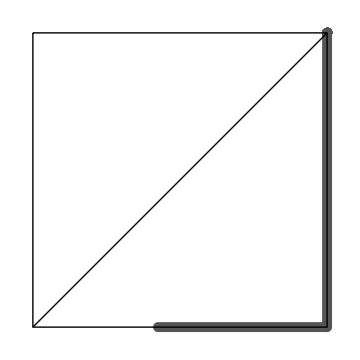

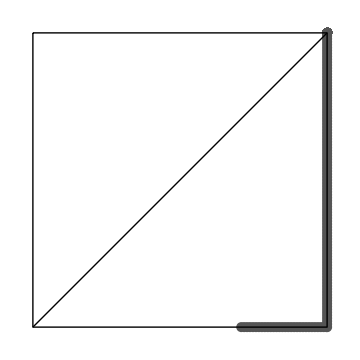

-Graphics-

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[0.02],Point[{#[[1]],#[[3]]}]}&,ω[[1]][[2;;]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[0.02],Point[{#[[1]],#[[3]]}]}&,ω[[2]]][[2;;]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[0.02],Point[{#[[1]],#[[3]]}]}&,ω[[3]]][[2;;]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```

## Model 3: Total Sperm Egg Dysfunction (Unviable Sperm)

## Dynamical Equations

g_i : growth function of population of class i.  6 classes in total: 
mex, lat, female wild-type hybrid, male wild-type hybrid, female mutant hybrid, male mutant hybrid.

```mathematica
g_(h1,♀)=(K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2-Subscript[Ψ, h])N_(h1,♀)+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀);
g_(h1,♂)=(K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2 N_(h1,♀)-Subscript[Ψ, h] N_(h1,♂))+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀);
g_(h2,♀)=((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-Subscript[Ψ, h])N_(h2,♀);
g_(h2,♂)=(1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂);
```

## Conditions for the Spread of a Partial Apomictic Mutant h2 at wt equilibrium

### For any values of β and σ

```mathematica
Reduce[(-(4 N_(h1,♀))/(Subscript[β, 2] (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh]))/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh]))<K≤(-(12 N_(h1,♀))/((1+Subscript[σ, 2]) (-1+Subscript[Φ, hh]))/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh]))&&K>0&&1>Subscript[c, p]>0&&1>Subscript[Φ, hh]>0&&1>Subscript[α, 2]>0&&1>Subscript[β, 2]>0&&1>Subscript[σ, 2]>-1,Subscript[σ, 2],Reals]//FullSimplify
```

0<α_2<1&&0<c_p<1&&Φ_hh>0&&√(-(-1+c_p) c_p)+Φ_hh<1&&1+√(1-(8 (-1+c_p) c_p)/(-1+Φ_hh)^2)<4 β_2&&β_2<1&&K>0&&1/β_2+√((1-(8 (-1+c_p) c_p)/(-1+Φ_hh)^2)/β_2^2)<2 (1+σ_2)&&σ_2<1

For a mutant to spread, 0<α_2, β_2>1/2 and σ_2>0 at least

#### β_2=1, σ_2=1

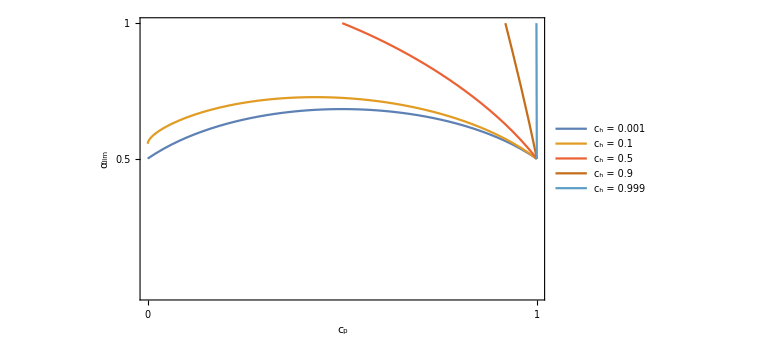

```mathematica
A1=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c, h]->0.001/.K->10/.Subscript[β, 2]->1/.Subscript[σ, 2]->1},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0.0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[1]],FrameStyle->Thick,FrameLabel->{"c_p","α_lim"},RotateLabel->False,PlotLegends->{"c_h = 0.001"},ImageSize->Large,LabelStyle->Directive[20,Bold,Black],FrameTicks->{{{0.5,1},None},{{0,1},None}}];
A2=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.1/.K->10/.Subscript[β, 2]->1/.Subscript[σ, 2]->1},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"c_h = 0.1"},LabelStyle->Directive[20,Bold,Black]];
A3=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.3/.K->10/.Subscript[β, 2]->1/.Subscript[σ, 2]->1},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[3]],PlotLegends->{"c_h = 0.3"},LabelStyle->Directive[20,Bold,Black]];
A4=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.5/.K->10/.Subscript[β, 2]->1/.Subscript[σ, 2]->1},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[4]],PlotLegends->{"c_h = 0.5"},LabelStyle->Directive[20,Bold,Black]];
A5=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.7/.K->10/.Subscript[β, 2]->1/.Subscript[σ, 2]->1},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[5]],PlotLegends->{"c_h = 0.7"},LabelStyle->Directive[20,Bold,Black]];
A6=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.9/.K->10/.Subscript[β, 2]->1/.Subscript[σ, 2]->1},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[6]],PlotLegends->{"c_h = 0.9"},LabelStyle->Directive[20,Bold,Black]];
A7=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c,h]->0.999/.K->10/.Subscript[β, 2]->1/.Subscript[σ, 2]->1},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[7]],PlotLegends->{"c_h = 0.999"},LabelStyle->Directive[20,Bold,Black]];
Fig=Show[{A1,A2,A4,A6,A7}]
```

#### β_2=3/4, σ_2=3/4

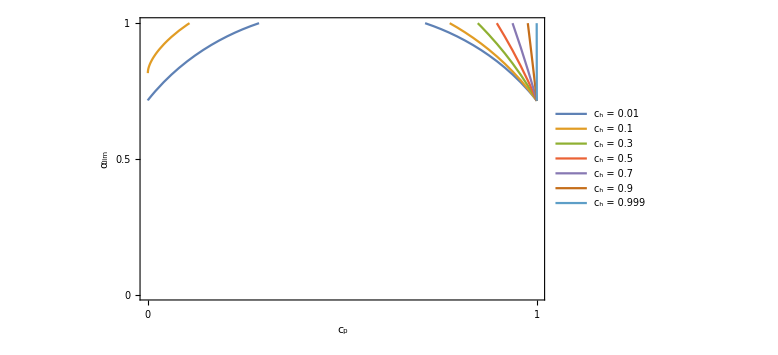

```mathematica
A1=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c, h]->0.001/.K->10/.Subscript[β, 2]->0.75/.Subscript[σ, 2]->0.75},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0.0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[1]],FrameStyle->Thick,FrameLabel->{"c_p","α_lim"},RotateLabel->False,PlotLegends->{"c_h = 0.01"},ImageSize->Large,LabelStyle->Directive[20,Bold,Black],FrameTicks->{{{0,0.5,1},None},{{0,1},None}}];
A2=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.1/.K->10/.Subscript[β, 2]->0.75/.Subscript[σ, 2]->0.75},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"c_h = 0.1"},LabelStyle->Directive[20,Bold,Black]];
A3=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.3/.K->10/.Subscript[β, 2]->0.75/.Subscript[σ, 2]->0.75},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[3]],PlotLegends->{"c_h = 0.3"},LabelStyle->Directive[20,Bold,Black]];
A4=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.5/.K->10/.Subscript[β, 2]->0.75/.Subscript[σ, 2]->0.75},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[4]],PlotLegends->{"c_h = 0.5"},LabelStyle->Directive[20,Bold,Black]];
A5=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.7/.K->10/.Subscript[β, 2]->0.75/.Subscript[σ, 2]->0.75},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[5]],PlotLegends->{"c_h = 0.7"},LabelStyle->Directive[20,Bold,Black]];
A6=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.9/.K->10/.Subscript[β, 2]->0.75/.Subscript[σ, 2]->0.75},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[6]],PlotLegends->{"c_h = 0.9"},LabelStyle->Directive[20,Bold,Black]];
A7=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c,h]->0.999/.K->10/.Subscript[β, 2]->0.75/.Subscript[σ, 2]->0.75},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[7]],PlotLegends->{"c_h = 0.999"},LabelStyle->Directive[20,Bold,Black]];
Fig=Show[{A1,A2,A3,A4,A5,A6,A7}]
```

#### β_2=0.7, σ_2=0.7

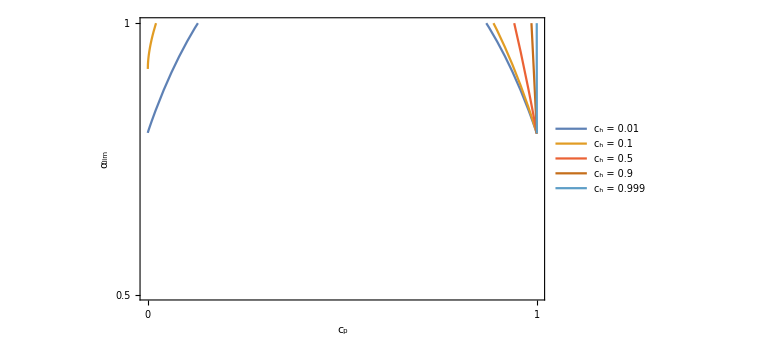

```mathematica
A1=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c, h]->0.001/.K->10/.Subscript[β, 2]->0.7/.Subscript[σ, 2]->0.7},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0.5,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[1]],FrameStyle->Thick,FrameLabel->{"c_p","α_lim"},RotateLabel->False,PlotLegends->{"c_h = 0.01"},ImageSize->Large,LabelStyle->Directive[20,Bold,Black],FrameTicks->{{{0.5,1},None},{{0,1},None}}];
A2=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.1/.K->10/.Subscript[β, 2]->0.7/.Subscript[σ, 2]->0.7},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"c_h = 0.1"},LabelStyle->Directive[20,Bold,Black]];
A3=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.3/.K->10/.Subscript[β, 2]->0.7/.Subscript[σ, 2]->0.7},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[3]],PlotLegends->{"c_h = 0.3"},LabelStyle->Directive[20,Bold,Black]];
A4=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.5/.K->10/.Subscript[β, 2]->0.7/.Subscript[σ, 2]->0.7},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[4]],PlotLegends->{"c_h = 0.5"},LabelStyle->Directive[20,Bold,Black]];
A5=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.7/.K->10/.Subscript[β, 2]->0.7/.Subscript[σ, 2]->0.7},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[5]],PlotLegends->{"c_h = 0.7"},LabelStyle->Directive[20,Bold,Black]];
A6=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/. Subscript[c, h]->0.9/.K->10/.Subscript[β, 2]->0.7/.Subscript[σ, 2]->0.7},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[6]],PlotLegends->{"c_h = 0.9"},LabelStyle->Directive[20,Bold,Black]];
A7=Plot[{(-1+Subscript[β, 2]-(8 N_(h1,♀))/(K (1+Subscript[σ, 2]) (-1+Subscript[Φ, hh])))/(-1+3 Subscript[β, 2])/.N_(h1,♀)->1/8 K (1+√(-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)-Subscript[Φ, hh])/.Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.Subscript[c,h]->0.999/.K->10/.Subscript[β, 2]->0.7/.Subscript[σ, 2]->0.7},{Subscript[c, p],0.0,1},PlotRange->{{0,1},{0,1}},Frame->True,PlotStyle->ColorData[97,"ColorList"][[7]],PlotLegends->{"c_h = 0.999"},LabelStyle->Directive[20,Bold,Black]];
Fig=Show[{A1,A2,A4,A6,A7}]
```

## Wild - Type - Mutant Equilibrium

When the first apomictic mutant spreads, it can reach an equilibrium that we found by solving the ODEs assuming that (1) N_(h1,♂) = N_(h1,♀), and (2) N_(h2,♂) = N_(h2,♀).

```mathematica
Dyn1=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,xf[0]==112.13083603191488,xm[0]==112.13083603191488,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn2=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.9/.Subscript[β, 2]->0.9/.Subscript[σ, 2]->0.9,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.9/.Subscript[β, 2]->0.9/.Subscript[σ, 2]->0.9,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.9/.Subscript[β, 2]->0.9/.Subscript[σ, 2]->0.9,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.9/.Subscript[β, 2]->0.9/.Subscript[σ, 2]->0.9,xf[0]==112.13083603191488,xm[0]==112.13083603191488,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn3=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.85/.Subscript[β, 2]->0.85/.Subscript[σ, 2]->0.85,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.85/.Subscript[β, 2]->0.85/.Subscript[σ, 2]->0.85,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.85/.Subscript[β, 2]->0.85/.Subscript[σ, 2]->0.85,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.1/.Subscript[c, p]->0.1/.Subscript[α, 2]->0.85/.Subscript[β, 2]->0.85/.Subscript[σ, 2]->0.85,xf[0]==112.13083603191488,xm[0]==112.13083603191488,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

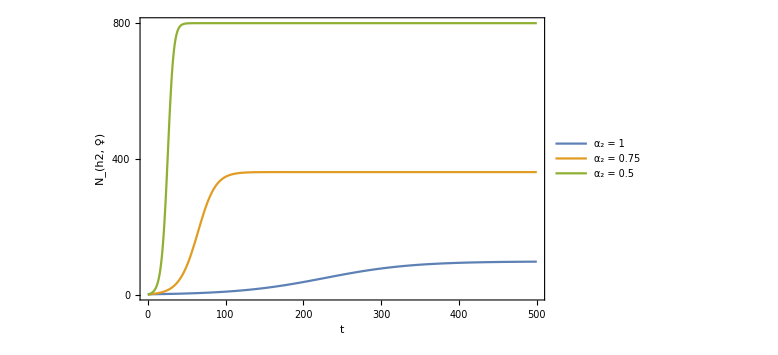

```mathematica
Plot[{Evaluate[yf[t]/.Dyn3],Evaluate[yf[t]/.Dyn2],Evaluate[yf[t]/.Dyn1]},{t,0,500},PlotRange->All,Frame->True,FrameStyle->Thick,FrameTicks->{{{0,400,800},None},{{0,100,200,300,400,500},None}},LabelStyle->Directive[Bold,18,Black],ImageSize->Large,FrameLabel->{"t","N_(h2, ♀)"},RotateLabel->False,PlotLegends->{"α_2 = 1","α_2 = 0.75","α_2 = 0.5"}]
```

```mathematica
Dyn1=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->1/.Subscript[β, 2]->1/.Subscript[σ, 2]->1,xf[0]==112.13083603191488,xm[0]==112.13083603191488,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn2=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.9/.Subscript[β, 2]->0.9/.Subscript[σ, 2]->0.9,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.9/.Subscript[β, 2]->0.9/.Subscript[σ, 2]->0.9,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.9/.Subscript[β, 2]->0.9/.Subscript[σ, 2]->0.9,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.9/.Subscript[β, 2]->0.9/.Subscript[σ, 2]->0.9,xf[0]==112.13083603191488,xm[0]==112.13083603191488,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

```mathematica
Dyn3=NDSolve[{D[xf[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2-(xf[t]+xm[t]+yf[t]+ym[t])/K)xf[t]+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.85/.Subscript[β, 2]->0.85/.Subscript[σ, 2]->0.85,D[xm[t],t]==(Subscript[c, p](1-Subscript[c, p])K)/4+((1-Subscript[Φ, hh])/2 xf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K xm[t])+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.85/.Subscript[β, 2]->0.85/.Subscript[σ, 2]->0.85,D[yf[t],t]==((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-(xf[t]+xm[t]+yf[t]+ym[t])/K)yf[t]/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.85/.Subscript[β, 2]->0.85/.Subscript[σ, 2]->0.85,D[ym[t],t]==((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))yf[t]-(xf[t]+xm[t]+yf[t]+ym[t])/K ym[t])/.Subscript[Φ, hh]->(Subscript[c, h](xm[t]+ym[t]))/(Subscript[c, h](xm[t]+ym[t])+(1-Subscript[c, h])(Subscript[c, p] K)/2)/.K->1000/.Subscript[c, h]->0.3/.Subscript[c, p]->0.9/.Subscript[α, 2]->0.85/.Subscript[β, 2]->0.85/.Subscript[σ, 2]->0.85,xf[0]==112.13083603191488,xm[0]==112.13083603191488,yf[0]==1,ym[0]==1},{xf,xm,yf,ym},{t,1,500}];
```

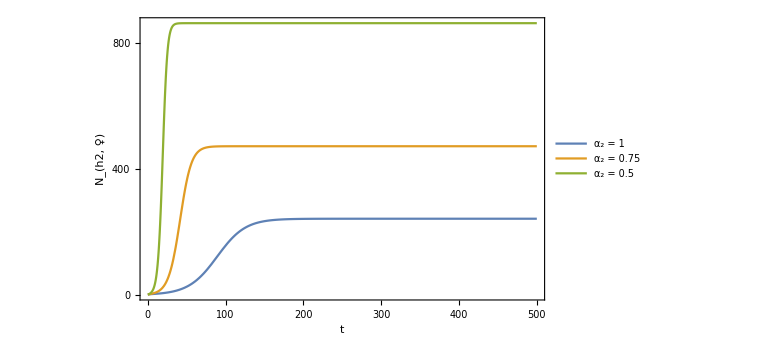

```mathematica
Plot[{Evaluate[yf[t]/.Dyn3],Evaluate[yf[t]/.Dyn2],Evaluate[yf[t]/.Dyn1]},{t,0,500},PlotRange->All,Frame->True,FrameStyle->Thick,FrameTicks->{{{0,400,800},None},{{0,100,200,300,400,500},None}},LabelStyle->Directive[Bold,18,Black],ImageSize->Large,FrameLabel->{"t","N_(h2, ♀)"},RotateLabel->False,PlotLegends->{"α_2 = 1","α_2 = 0.75","α_2 = 0.5"}]
```

## Evolutionary Routes

### c_p = 0.1

```mathematica
CP=0.1;
CH={0.01,0.2,0.4};
ω=Table[{0,0,0},{j,1,3},{i,1,1000}];
For[j=1,j<4,++j,
(*Print[j];*)
XOK=False;
While[XOK==False,
X0=(-1+ω[[j]][[1]][[2]]-(8 N_(h1,♀))/(K (1+ω[[j]][[1]][[3]]) (-1+Subscript[Φ, hh])))/(-1+3 ω[[j]][[1]][[2]])-ω[[j]][[1]][[1]]/.N_(h1,♀)->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]],K->10};
If[(X0>0)&&ω[[j]][[1]][[1]]≤1,
ω[[j]][[1]][[1]]=ω[[j]][[1]][[1]]+0.001;
ω[[j]][[1]][[2]]=ω[[j]][[1]][[2]]+0.001;
ω[[j]][[1]][[3]]=ω[[j]][[1]][[3]]+0.001;,
Sol=Solve[((K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2-Subscript[Ψ, h])N_(h1,♀)+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[1]][[1]],Subscript[β, 2]->ω[[j]][[1]][[2]],Subscript[σ, 2]->ω[[j]][[1]][[3]]})==0&&((K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2 N_(h1,♀)-Subscript[Ψ, h] N_(h1,♂))+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[1]][[1]],Subscript[β, 2]->ω[[j]][[1]][[2]],Subscript[σ, 2]->ω[[j]][[1]][[3]]})==0&&(((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-Subscript[Ψ, h])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[1]][[1]],Subscript[β, 2]->ω[[j]][[1]][[2]],Subscript[σ, 2]->ω[[j]][[1]][[3]]})==0&&((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[1]][[1]],Subscript[β, 2]->ω[[j]][[1]][[2]],Subscript[σ, 2]->ω[[j]][[1]][[3]]})==0&&N_(h1,♀)>0&&N_(h2,♀)>0&&N_(h1,♂)>0&&N_(h2,♂)>0,{N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=Length[Sol];
If[NumbSol==0&&ω[[j]][[1]][[1]]≤1,
ω[[j]][[1]][[1]]=ω[[j]][[1]][[1]]+0.001;
ω[[j]][[1]][[2]]=ω[[j]][[1]][[2]]+0.001;
ω[[j]][[1]][[3]]=ω[[j]][[1]][[3]]+0.001,
XOK=True]]];
(*Print[ω[[j]][[1]][[1]]];
Print[ω[[j]][[1]][[2]]];
Print[ω[[j]][[1]][[3]]];*)
If[(XOK==True)&&ω[[j]][[1]][[1]]≤1,
ϕ=Table[0,{i,1,1000}];
g=(1+Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3] Subscript[β, 3](1-Subscript[Φ, hh]));
D1=D[g/.Subscript[β, 3] ->Subscript[β, 2]/.Subscript[σ, 3]->Subscript[σ, 2],Subscript[α, 3]];
D2=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[σ, 3]->Subscript[σ, 2],Subscript[β, 3]];
D3=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[β, 3]->Subscript[β, 2],Subscript[σ, 3]];
For[i=1,i<1000,i++,
Nh = 0;
Sol=Solve[((K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2-Subscript[Ψ, h])N_(h1,♀)+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2 N_(h1,♀)-Subscript[Ψ, h] N_(h1,♂))+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&(((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-Subscript[Ψ, h])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&N_(h1,♀)>0&&N_(h2,♀)>0&&N_(h1,♂)>0&&N_(h2,♂)>0,{N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=Length[Sol];
If[NumbSol==1,Nh=(N_(h1,♀)/.Sol[[1]])+(N_(h2,♂)/.Sol[[1]]);
ϕ[[i]]=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10;
If[ω[[j]][[i]][[1]]<1,Direc1=D1/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc1=0];
If[ω[[j]][[i]][[2]]<1,Direc2=D2/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc2=0];
If[ω[[j]][[i]][[3]]<1,Direc3=D3/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc3=0];
Direc=Max[Abs[Direc1],Abs[Direc2],Abs[Direc3]];
υ=1/1000;
If[Direc==Abs[Direc1]&&Direc≠Abs[Direc2],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc2]&&Direc≠Abs[Direc1],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]]+υ*Sign[Direc2];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc1]&&Direc==Abs[Direc2],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]]+υ*Sign[Direc2];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc3],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]+υ*Sign[Direc3]];
If[ω[[j]][[i+1]][[1]]>1,ω[[j]][[i+1]][[1]]=1];
If[ω[[j]][[i+1]][[1]]<0,ω[[j]][[i+1]][[1]]=0];
If[ω[[j]][[i+1]][[2]]>1,ω[[j]][[i+1]][[2]]=1];
If[ω[[j]][[i+1]][[2]]<0,ω[[j]][[i+1]][[2]]=0];
If[ω[[j]][[i+1]][[3]]>1,ω[[j]][[i+1]][[3]]=1];
If[ω[[j]][[i+1]][[3]]<-1,ω[[j]][[i+1]][[3]]=-1]
(*,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]*)]]]];
Plot3=ListPointPlot3D[{ω[[1]],ω[[2]],ω[[3]]},AxesLabel->{"α","β","σ"},PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[PointSize[0.007],Opacity[0.8]],LabelStyle->Directive[Black,Bold],ImageSize->Large,PlotLegends->{"c_h = 0.01","c_h = 0.2","c_h = 0.4"},PlotLabel->"c_p = 0.1"]
```

Transforming that into a 2 D space with the size of the points taking into account the α dimension :

```mathematica
ω[[1]]=DeleteCases[ω[[1]],{0,0,0}];
ω[[2]]=DeleteCases[ω[[2]],{0,0,0}];
ω[[3]]=DeleteCases[ω[[3]],{0,0,0}];
```

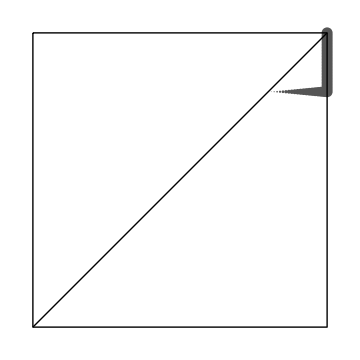

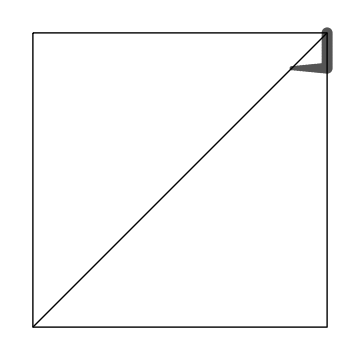

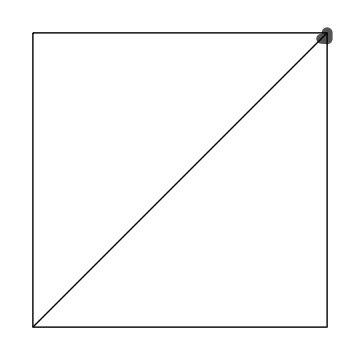

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[1]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[2]]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[3]]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```

Changing the axis origin:

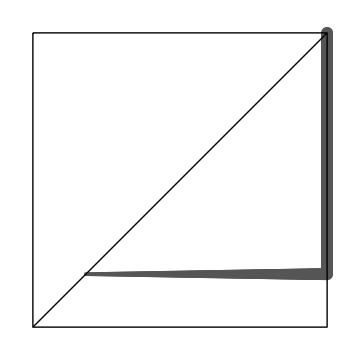

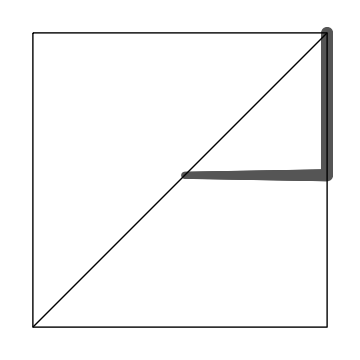

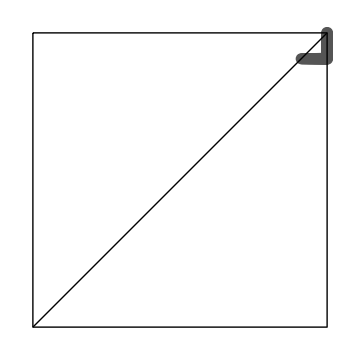

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.7)*0.08],Point[{4*(#[[2]]-0.75),4*(#[[3]]-0.75)}]}&,ω[[1]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.7)*0.08],Point[{4*(#[[2]]-0.75),4*(#[[3]]-0.75)}]}&,ω[[2]]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.7)*0.08],Point[{4*(#[[2]]-0.75),4*(#[[3]]-0.75)}]}&,ω[[3]]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```

### c_p = 0.5

```mathematica
CP=0.5;
CH={0.01,0.2,0.4};
ω=Table[{0.34,0.34,0.34},{j,1,3},{i,1,1000}];
For[j=1,j<4,++j,
(*Print[j];*)
XOK=False;
While[XOK==False,
X0=(-1+ω[[j]][[1]][[2]]-(8 N_(h1,♀))/(K (1+ω[[j]][[1]][[3]]) (-1+Subscript[Φ, hh])))/(-1+3 ω[[j]][[1]][[2]])-ω[[j]][[1]][[1]]/.N_(h1,♀)->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]],K->100};
If[(X0>0)&&ω[[j]][[1]][[1]]≤1,
ω[[j]][[1]][[1]]=ω[[j]][[1]][[1]]+0.001;
ω[[j]][[1]][[2]]=ω[[j]][[1]][[2]]+0.001;
ω[[j]][[1]][[3]]=ω[[j]][[1]][[3]]+0.001;,
XOK=True]];
(*Print[ω[[j]][[1]][[1]]];
Print[ω[[j]][[1]][[2]]];
Print[ω[[j]][[1]][[3]]];*)
If[(XOK==True)&&ω[[j]][[1]][[1]]≤1,
ϕ=Table[0,{i,1,1000}];
g=(1+Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3] Subscript[β, 3](1-Subscript[Φ, hh]));
D1=D[g/.Subscript[β, 3] ->Subscript[β, 2]/.Subscript[σ, 3]->Subscript[σ, 2],Subscript[α, 3]];
D2=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[σ, 3]->Subscript[σ, 2],Subscript[β, 3]];
D3=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[β, 3]->Subscript[β, 2],Subscript[σ, 3]];
For[i=1,i<1000,i++,
Nh = 0;
Sol=Solve[((K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2-Subscript[Ψ, h])N_(h1,♀)+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2 N_(h1,♀)-Subscript[Ψ, h] N_(h1,♂))+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&(((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-Subscript[Ψ, h])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&N_(h1,♀)>0&&N_(h2,♀)>0&&N_(h1,♂)>0&&N_(h2,♂)>0,{N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=Length[Sol];
If[NumbSol==1,Nh=(N_(h1,♀)/.Sol[[1]])+(N_(h2,♂)/.Sol[[1]]);
ϕ[[i]]=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10;
If[ω[[j]][[i]][[1]]<1,Direc1=D1/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc1=0];
If[ω[[j]][[i]][[2]]<1,Direc2=D2/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc2=0];
If[ω[[j]][[i]][[3]]<1,Direc3=D3/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc3=0];
Direc=Max[Abs[Direc1],Abs[Direc2],Abs[Direc3]];
υ=1/1000;
If[Direc==Abs[Direc1]&&Direc≠Abs[Direc2],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc2]&&Direc≠Abs[Direc1],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]]+υ*Sign[Direc2];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc1]&&Direc==Abs[Direc2],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]]+υ*Sign[Direc2];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc3],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]+υ*Sign[Direc3]];
If[ω[[j]][[i+1]][[1]]>1,ω[[j]][[i+1]][[1]]=1];
If[ω[[j]][[i+1]][[1]]<0,ω[[j]][[i+1]][[1]]=0];
If[ω[[j]][[i+1]][[2]]>1,ω[[j]][[i+1]][[2]]=1];
If[ω[[j]][[i+1]][[2]]<0,ω[[j]][[i+1]][[2]]=0];
If[ω[[j]][[i+1]][[3]]>1,ω[[j]][[i+1]][[3]]=1];
If[ω[[j]][[i+1]][[3]]<-1,ω[[j]][[i+1]][[3]]=-1]
(*,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]*)]]]];
Plot3=ListPointPlot3D[{ω[[1]],ω[[2]],ω[[3]]},AxesLabel->{"α","β","σ"},PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[PointSize[0.007],Opacity[0.8]],LabelStyle->Directive[Black,Bold],ImageSize->Large,PlotLegends->{"c_h = 0.01","c_h = 0.2","c_h = 0.4"},PlotLabel->"c_p = 0.5"];
```

```mathematica
ω[[1]]=DeleteCases[ω[[1]],{0.34,0.34,0.34}];
ω[[2]]=DeleteCases[ω[[2]],{0.34,0.34,0.34}];
ω[[3]]=DeleteCases[ω[[3]],{0.34,0.34,0.34}];
```

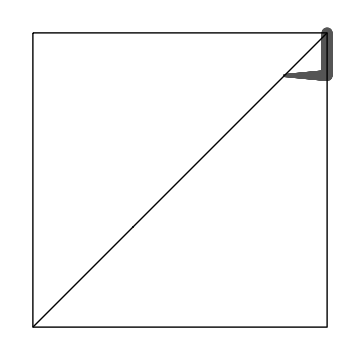

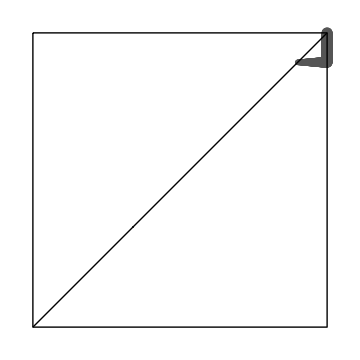

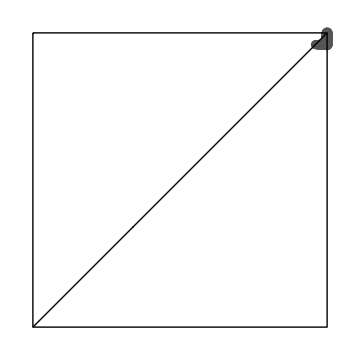

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[1]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[2]]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[3]]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```

Changing the axis origin:

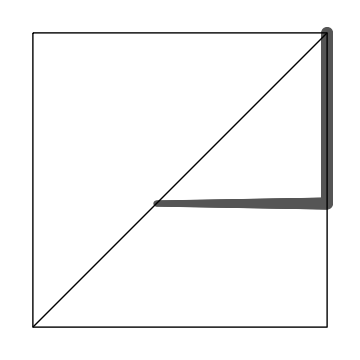

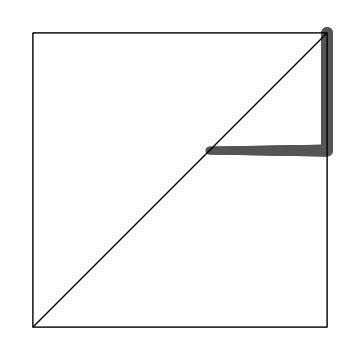

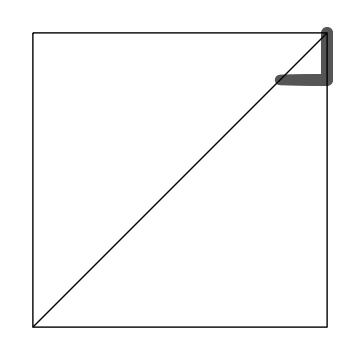

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.7)*0.08],Point[{4*(#[[2]]-0.75),4*(#[[3]]-0.75)}]}&,ω[[1]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.7)*0.08],Point[{4*(#[[2]]-0.75),4*(#[[3]]-0.75)}]}&,ω[[2]]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.7)*0.08],Point[{4*(#[[2]]-0.75),4*(#[[3]]-0.75)}]}&,ω[[3]]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```

### c_p = 0.9

```mathematica
CP=0.9;
CH={0.1,0.6,0.8};
ω=Table[{0.34,0.34,0.34},{j,1,3},{i,1,1000}];
For[j=1,j<4,++j,
(*Print[j];*)
XOK=False;
While[XOK==False,
X0=(-1+ω[[j]][[1]][[2]]-(8 N_(h1,♀))/(K (1+ω[[j]][[1]][[3]]) (-1+Subscript[Φ, hh])))/(-1+3 ω[[j]][[1]][[2]])-ω[[j]][[1]][[1]]/.N_(h1,♀)->(K/8) (1+√ (-8 (-1+Subscript[c, p]) Subscript[c, p]+(-1+Subscript[Φ, hh])^2)- Subscript[Φ, hh])/. Subscript[Φ, hh]->Root[-Subscript[c, h]^2+#1^3 (-Subscript[c, h]+Subscript[c, h]^2)+Subscript[c, h]^2 Subscript[c, p]+#1 (-Subscript[c, h]+3 Subscript[c, h]^2-2 Subscript[c, h]^2 Subscript[c, p])+#1^2 (2 Subscript[c, h]-3 Subscript[c, h]^2+2 Subscript[c, p]-4 Subscript[c, h] Subscript[c, p]+3 Subscript[c, h]^2 Subscript[c, p])&,2]/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]],K->100};
If[(X0>0)&&ω[[j]][[1]][[1]]≤1,
ω[[j]][[1]][[1]]=ω[[j]][[1]][[1]]+0.001;
ω[[j]][[1]][[2]]=ω[[j]][[1]][[2]]+0.001;
ω[[j]][[1]][[3]]=ω[[j]][[1]][[3]]+0.001;,
XOK=True]];
(*Print[ω[[j]][[1]][[1]]];
Print[ω[[j]][[1]][[2]]];
Print[ω[[j]][[1]][[3]]];*)
If[(XOK==True)&&ω[[j]][[1]][[1]]≤1,
ϕ=Table[0,{i,1,1000}];
g=(1+Subscript[σ, 3])/2(((1-Subscript[α, 3])(1-Subscript[β, 3]))/2(1-Subscript[Φ, hh])+Subscript[α, 3] Subscript[β, 3](1-Subscript[Φ, hh]));
D1=D[g/.Subscript[β, 3] ->Subscript[β, 2]/.Subscript[σ, 3]->Subscript[σ, 2],Subscript[α, 3]];
D2=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[σ, 3]->Subscript[σ, 2],Subscript[β, 3]];
D3=D[g/.Subscript[α, 3]->Subscript[α, 2]/.Subscript[β, 3]->Subscript[β, 2],Subscript[σ, 3]];
For[i=1,i<1000,i++,
Nh = 0;
Sol=Solve[((K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2-Subscript[Ψ, h])N_(h1,♀)+(1+Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((K Subscript[c, p](1-Subscript[c, p]))/4+((1-Subscript[Φ, hh])/2 N_(h1,♀)-Subscript[Ψ, h] N_(h1,♂))+(1-Subscript[σ, 2])/4(1-Subscript[α, 2])(1-Subscript[β, 2])(1-Subscript[Φ, hh])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&(((1+Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))-Subscript[Ψ, h])N_(h2,♀)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&((1-Subscript[σ, 2])/2(((1-Subscript[α, 2])(1-Subscript[β, 2]))/2(1-Subscript[Φ, hh])+Subscript[α, 2] Subscript[β, 2](1-Subscript[Φ, hh]))N_(h2,♀)-Subscript[Ψ, h] N_(h2,♂)/.Subscript[Φ, hh]->(Subscript[c, h](N_(h1,♂)+N_(h2,♂)))/(Subscript[c, h](N_(h1,♂)+N_(h2,♂))+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]})==0&&N_(h1,♀)>0&&N_(h2,♀)>0&&N_(h1,♂)>0&&N_(h2,♂)>0,{N_(h1,♀),N_(h1,♂),N_(h2,♀),N_(h2,♂)}];
NumbSol=Length[Sol];
If[NumbSol==1,Nh=(N_(h1,♀)/.Sol[[1]])+(N_(h2,♂)/.Sol[[1]]);
ϕ[[i]]=(Subscript[c, h] Nh)/(Subscript[c, h] Nh+(1-Subscript[c, h])((Subscript[c, p] K)/2))/.{Subscript[c, p]->CP,Subscript[c, h]->CH[[j]]}/.K->10;
If[ω[[j]][[i]][[1]]<1,Direc1=D1/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc1=0];
If[ω[[j]][[i]][[2]]<1,Direc2=D2/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc2=0];
If[ω[[j]][[i]][[3]]<1,Direc3=D3/.Subscript[Φ, hh]->ϕ[[i]]/.{Subscript[α, 2]->ω[[j]][[i]][[1]],Subscript[β, 2]->ω[[j]][[i]][[2]],Subscript[σ, 2]->ω[[j]][[i]][[3]]},Direc3=0];
Direc=Max[Abs[Direc1],Abs[Direc2],Abs[Direc3]];
υ=1/1000;
If[Direc==Abs[Direc1]&&Direc≠Abs[Direc2],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc2]&&Direc≠Abs[Direc1],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]]+υ*Sign[Direc2];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc1]&&Direc==Abs[Direc2],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]]+υ*Sign[Direc1];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]]+υ*Sign[Direc2];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]];
If[Direc==Abs[Direc3],ω[[j]][[i+1]][[1]]=ω[[j]][[i]][[1]];
ω[[j]][[i+1]][[2]]=ω[[j]][[i]][[2]];
ω[[j]][[i+1]][[3]]=ω[[j]][[i]][[3]]+υ*Sign[Direc3]];
If[ω[[j]][[i+1]][[1]]>1,ω[[j]][[i+1]][[1]]=1];
If[ω[[j]][[i+1]][[1]]<0,ω[[j]][[i+1]][[1]]=0];
If[ω[[j]][[i+1]][[2]]>1,ω[[j]][[i+1]][[2]]=1];
If[ω[[j]][[i+1]][[2]]<0,ω[[j]][[i+1]][[2]]=0];
If[ω[[j]][[i+1]][[3]]>1,ω[[j]][[i+1]][[3]]=1];
If[ω[[j]][[i+1]][[3]]<-1,ω[[j]][[i+1]][[3]]=-1]
(*,Print["ERROR:"] ;Print[ NumbSol];Print[ "equilibria possible"]*)]]]];
Plot3=ListPointPlot3D[{ω[[1]],ω[[2]],ω[[3]]},AxesLabel->{"α","β","σ"},PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[PointSize[0.007],Opacity[0.8]],LabelStyle->Directive[Black,Bold],ImageSize->Large,PlotLegends->{"c_h = 0.1","c_h = 0.6","c_h = 0.8"},PlotLabel->"c_p = 0.9"];
```

```mathematica
ω[[1]]=DeleteCases[ω[[1]],{0.34,0.34,0.34}];
ω[[2]]=DeleteCases[ω[[2]],{0.34,0.34,0.34}];
ω[[3]]=DeleteCases[ω[[3]],{0.34,0.34,0.34}];
```

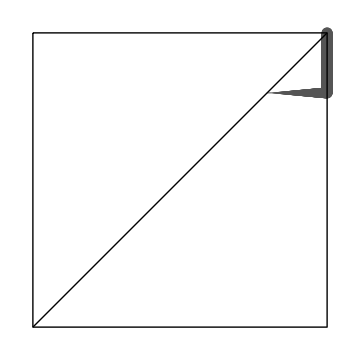

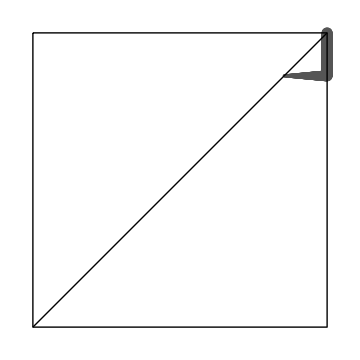

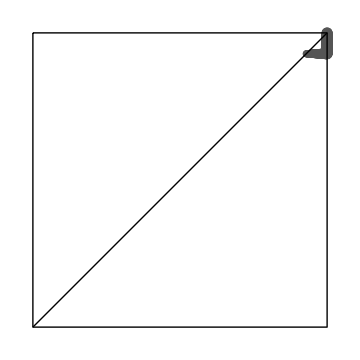

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[1]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[2]]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.8)*0.11],Point[{#[[2]],#[[3]]}]}&,ω[[3]]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```

Changing the axis origin:

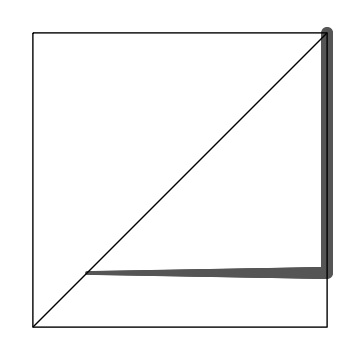

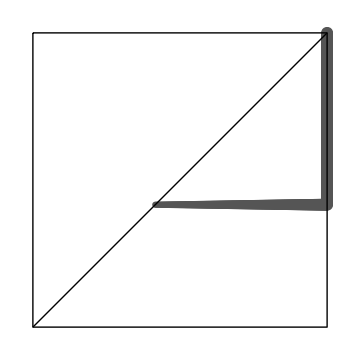

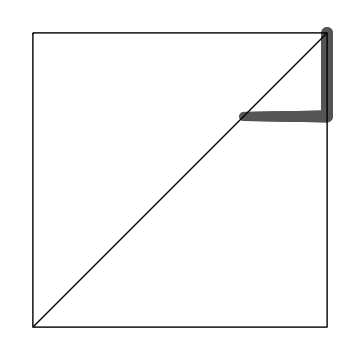

```mathematica
P11=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.7)*0.08],Point[{4*(#[[2]]-0.75),4*(#[[3]]-0.75)}]}&,ω[[1]]],AspectRatio->1,ImageSize->Medium];
P12=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.7)*0.08],Point[{4*(#[[2]]-0.75),4*(#[[3]]-0.75)}]}&,ω[[2]]],AspectRatio->1,ImageSize->Medium];
P13=Graphics[Map[{Lighter[Black],PointSize[(#[[1]]-0.7)*0.08],Point[{4*(#[[2]]-0.75),4*(#[[3]]-0.75)}]}&,ω[[3]]],AspectRatio->1,ImageSize->Medium];
P3=Graphics[Line[{{0,1},{0,0},{1,0},{1,1},{0,1}}]];
P4=Graphics[Line[{{0,0},{1,1}}]];
A=Show[{P11,P3,P4}]
B=Show[{P12,P3,P4}]
F=Show[{P13,P3,P4}]
```